```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,10,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

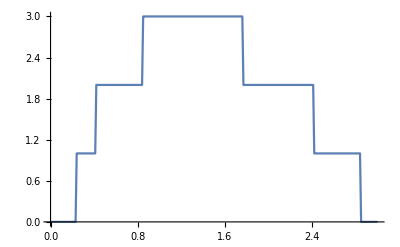

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,3,0.01}]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,3,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},3],Table[imp,17]]]
```

{imp,imp,imp,imp1,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp}

```mathematica
m2[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp1,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/1imp.dat",Table[{ω,Mean[ParallelTable[m2[ω,0.5],10000]]},{ω,Range[0,3,0.01]}]]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/1imp.dat

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},9],Table[imp,11]]]
```

{imp,imp1,imp,imp,imp7,imp13,imp6,imp,imp,imp,imp,imp4,imp9,imp5,imp2,imp,imp,imp,imp14,imp}

```mathematica
m3[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp1,imp,imp,imp7,imp13,imp6,imp,imp,imp,imp,imp4,imp9,imp5,imp2,imp,imp,imp,imp14,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},12],Table[imp,8]]]
```

{imp11,imp14,imp,imp,imp5,imp10,imp,imp,imp2,imp1,imp,imp,imp3,imp12,imp,imp13,imp6,imp,imp9,imp7}

```mathematica
m4[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp11,imp14,imp,imp,imp5,imp10,imp,imp,imp2,imp1,imp,imp,imp3,imp12,imp,imp13,imp6,imp,imp9,imp7}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},14],Table[imp,6]]]
```

{imp1,imp,imp,imp,imp4,imp13,imp9,imp11,imp,imp,imp8,imp7,imp5,imp3,imp,imp6,imp12,imp14,imp2,imp10}

```mathematica
m5[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp,imp,imp,imp4,imp13,imp9,imp11,imp,imp,imp8,imp7,imp5,imp3,imp,imp6,imp12,imp14,imp2,imp10}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13,imp15,imp16,imp17}],Table[imp,3]]]
```

{imp10,imp,imp5,imp6,imp12,imp16,imp14,imp17,imp4,imp7,imp13,imp15,imp,imp8,imp11,imp9,imp2,imp3,imp1,imp}

```mathematica
m6[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{1,14}],μ16=RandomInteger[{1,14}],μ17=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]],
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]],
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp10,imp,imp5,imp6,imp12,imp16,imp14,imp17,imp4,imp7,imp13,imp15,imp,imp8,imp11,imp9,imp2,imp3,imp1,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13,imp15,imp16,imp17}],{imp1,imp2,imp3},Table[imp,0]]]
```

{imp9,imp2,imp13,imp17,imp2,imp3,imp5,imp7,imp14,imp3,imp1,imp6,imp4,imp1,imp15,imp16,imp10,imp11,imp8,imp12}

```mathematica
m7[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{1,14}],μ16=RandomInteger[{1,14}],μ17=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]],
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]],
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp9,imp2,imp13,imp17,imp2,imp3,imp5,imp7,imp14,imp3,imp1,imp6,imp4,imp1,imp15,imp16,imp10,imp11,imp8,imp12}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m2[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m3[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m4[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m5[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m6[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m7[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.69165×10^-7},{0.01,2.48306×10^-7},{0.02,2.54539×10^-7},{0.03,2.62091×10^-7},{0.04,2.7055×10^-7},{0.05,2.79067×10^-7},{0.06,2.88781×10^-7},{0.07,3.04072×10^-7},{0.08,3.18149×10^-7},{0.09,3.35256×10^-7},{0.1,3.5488×10^-7},{0.11,3.8815×10^-7},{0.12,4.24423×10^-7},{0.13,4.74282×10^-7},{0.14,5.43166×10^-7},{0.15,6.31211×10^-7},{0.16,7.53494×10^-7},{0.17,9.26023×10^-7},{0.18,1.2006×10^-6},{0.19,1.65416×10^-6},{0.2,2.52267×10^-6},{0.21,4.56877×10^-6},{0.22,0.0000117889},{0.23,0.000102506},{0.24,0.134124},{0.25,0.615139},{0.26,0.755346},{0.27,0.81635},{0.28,0.85487},{0.29,0.876502},{0.3,0.885114},{0.31,0.898519},{0.32,0.906263},{0.33,0.908453},{0.34,0.91376},{0.35,0.915796},{0.36,0.916618},{0.37,0.915159},{0.38,0.914396},{0.39,0.908573},{0.4,0.882614},{0.41,0.78692},{0.42,0.619217},{0.43,1.00236},{0.44,1.29545},{0.45,1.44687},{0.46,1.55119},{0.47,1.6111},{0.48,1.65213},{0.49,1.67686},{0.5,1.70647},{0.51,1.728},{0.52,1.73514},{0.53,1.75306},{0.54,1.7617},{0.55,1.7855},{0.56,1.78416},{0.57,1.79252},{0.58,1.79919},{0.59,1.80101},{0.6,1.81016},{0.61,1.8159},{0.62,1.81682},{0.63,1.82278},{0.64,1.82782},{0.65,1.82589},{0.66,1.8335},{0.67,1.83151},{0.68,1.83518},{0.69,1.83759},{0.7,1.83837},{0.71,1.84123},{0.72,1.84758},{0.73,1.85108},{0.74,1.84747},{0.75,1.84571},{0.76,1.85663},{0.77,1.85043},{0.78,1.85464},{0.79,1.85372},{0.8,1.85651},{0.81,1.85652},{0.82,1.84513},{0.83,1.83394},{0.84,1.77613},{0.85,1.03182},{0.86,1.42589},{0.87,1.85222},{0.88,2.13822},{0.89,2.28562},{0.9,2.34705},{0.91,2.44243},{0.92,2.47326},{0.93,2.53345},{0.94,2.57084},{0.95,2.60032},{0.96,2.6153},{0.97,2.63603},{0.98,2.67334},{0.99,2.68002},{1.,2.69223},{1.01,2.70934},{1.02,2.678},{1.03,2.58098},{1.04,2.30205},{1.05,1.63889},{1.06,0.873168},{1.07,0.865573},{1.08,1.31902},{1.09,1.65418},{1.1,1.89178},{1.11,2.02769},{1.12,2.12241},{1.13,2.1926},{1.14,2.26},{1.15,2.29396},{1.16,2.33791},{1.17,2.34839},{1.18,2.38004},{1.19,2.38825},{1.2,2.41205},{1.21,2.41983},{1.22,2.43316},{1.23,2.45189},{1.24,2.43768},{1.25,2.45485},{1.26,2.45265},{1.27,2.45224},{1.28,2.45525},{1.29,2.45041},{1.3,2.47434},{1.31,2.46615},{1.32,2.46264},{1.33,2.47054},{1.34,2.45917},{1.35,2.46784},{1.36,2.46758},{1.37,2.47665},{1.38,2.46537},{1.39,2.45905},{1.4,2.45348},{1.41,2.45291},{1.42,2.44358},{1.43,2.43816},{1.44,2.44502},{1.45,2.4265},{1.46,2.42534},{1.47,2.42875},{1.48,2.41997},{1.49,2.41399},{1.5,2.4183},{1.51,2.40801},{1.52,2.39857},{1.53,2.38237},{1.54,2.37409},{1.55,2.35558},{1.56,2.33808},{1.57,2.32896},{1.58,2.30508},{1.59,2.28427},{1.6,2.25967},{1.61,2.2552},{1.62,2.22736},{1.63,2.21726},{1.64,2.19548},{1.65,2.16623},{1.66,2.12038},{1.67,2.06476},{1.68,2.03043},{1.69,1.99779},{1.7,1.88858},{1.71,1.8308},{1.72,1.70133},{1.73,1.56696},{1.74,1.42671},{1.75,1.11472},{1.76,0.984431},{1.77,1.18569},{1.78,1.15532},{1.79,1.09317},{1.8,1.19045},{1.81,1.36809},{1.82,1.48827},{1.83,1.55721},{1.84,1.618},{1.85,1.6485},{1.86,1.67384},{1.87,1.68356},{1.88,1.6932},{1.89,1.70384},{1.9,1.70884},{1.91,1.71394},{1.92,1.71212},{1.93,1.71798},{1.94,1.71798},{1.95,1.72323},{1.96,1.71934},{1.97,1.7153},{1.98,1.71918},{1.99,1.71851},{2.,1.71083},{2.01,1.7133},{2.02,1.71043},{2.03,1.71333},{2.04,1.70813},{2.05,1.70971},{2.06,1.70454},{2.07,1.69728},{2.08,1.69853},{2.09,1.69793},{2.1,1.68919},{2.11,1.68615},{2.12,1.69931},{2.13,1.67696},{2.14,1.67554},{2.15,1.67285},{2.16,1.66867},{2.17,1.65308},{2.18,1.65437},{2.19,1.64292},{2.2,1.64038},{2.21,1.62809},{2.22,1.61083},{2.23,1.59575},{2.24,1.60581},{2.25,1.57928},{2.26,1.56643},{2.27,1.56051},{2.28,1.5449},{2.29,1.53318},{2.3,1.5055},{2.31,1.48548},{2.32,1.45384},{2.33,1.42651},{2.34,1.39461},{2.35,1.35621},{2.36,1.29359},{2.37,1.23953},{2.38,1.14685},{2.39,1.03247},{2.4,0.844504},{2.41,0.650813},{2.42,0.645416},{2.43,0.53712},{2.44,0.546911},{2.45,0.623483},{2.46,0.699919},{2.47,0.751524},{2.48,0.786709},{2.49,0.815408},{2.5,0.825286},{2.51,0.827966},{2.52,0.833306},{2.53,0.839625},{2.54,0.830947},{2.55,0.838483},{2.56,0.839379},{2.57,0.833396},{2.58,0.838018},{2.59,0.831316},{2.6,0.831983},{2.61,0.828689},{2.62,0.824957},{2.63,0.817076},{2.64,0.823291},{2.65,0.80821},{2.66,0.814587},{2.67,0.802658},{2.68,0.801105},{2.69,0.787132},{2.7,0.77774},{2.71,0.768223},{2.72,0.763676},{2.73,0.752147},{2.74,0.729233},{2.75,0.725346},{2.76,0.703829},{2.77,0.682219},{2.78,0.655818},{2.79,0.632177},{2.8,0.595269},{2.81,0.555575},{2.82,0.484379},{2.83,0.404814},{2.84,0.29077},{2.85,0.000382919},{2.86,0.000016172},{2.87,4.85004×10^-6},{2.88,2.28022×10^-6},{2.89,1.31314×10^-6},{2.9,8.38133×10^-7},{2.91,5.85991×10^-7},{2.92,4.36829×10^-7},{2.93,3.41448×10^-7},{2.94,2.72955×10^-7},{2.95,2.23132×10^-7},{2.96,1.84874×10^-7},{2.97,1.54748×10^-7},{2.98,1.31253×10^-7},{2.99,1.12523×10^-7},{3.,9.90302×10^-8}}

{{0.,2.69165×10^-7},{0.01,2.48306×10^-7},{0.02,2.54539×10^-7},{0.03,2.62091×10^-7},{0.04,2.7055×10^-7},{0.05,2.79067×10^-7},{0.06,2.88781×10^-7},{0.07,3.04072×10^-7},{0.08,3.18149×10^-7},{0.09,3.35256×10^-7},{0.1,3.5488×10^-7},{0.11,3.8815×10^-7},{0.12,4.24423×10^-7},{0.13,4.74282×10^-7},{0.14,5.43166×10^-7},{0.15,6.31211×10^-7},{0.16,7.53494×10^-7},{0.17,9.26023×10^-7},{0.18,1.2006×10^-6},{0.19,1.65416×10^-6},{0.2,2.52267×10^-6},{0.21,4.56877×10^-6},{0.22,0.0000117889},{0.23,0.000102506},{0.24,0.134124},{0.25,0.615139},{0.26,0.755346},{0.27,0.81635},{0.28,0.85487},{0.29,0.876502},{0.3,0.885114},{0.31,0.898519},{0.32,0.906263},{0.33,0.908453},{0.34,0.91376},{0.35,0.915796},{0.36,0.916618},{0.37,0.915159},{0.38,0.914396},{0.39,0.908573},{0.4,0.882614},{0.41,0.78692},{0.42,0.619217},{0.43,1.00236},{0.44,1.29545},{0.45,1.44687},{0.46,1.55119},{0.47,1.6111},{0.48,1.65213},{0.49,1.67686},{0.5,1.70647},{0.51,1.728},{0.52,1.73514},{0.53,1.75306},{0.54,1.7617},{0.55,1.7855},{0.56,1.78416},{0.57,1.79252},{0.58,1.79919},{0.59,1.80101},{0.6,1.81016},{0.61,1.8159},{0.62,1.81682},{0.63,1.82278},{0.64,1.82782},{0.65,1.82589},{0.66,1.8335},{0.67,1.83151},{0.68,1.83518},{0.69,1.83759},{0.7,1.83837},{0.71,1.84123},{0.72,1.84758},{0.73,1.85108},{0.74,1.84747},{0.75,1.84571},{0.76,1.85663},{0.77,1.85043},{0.78,1.85464},{0.79,1.85372},{0.8,1.85651},{0.81,1.85652},{0.82,1.84513},{0.83,1.83394},{0.84,1.77613},{0.85,1.03182},{0.86,1.42589},{0.87,1.85222},{0.88,2.13822},{0.89,2.28562},{0.9,2.34705},{0.91,2.44243},{0.92,2.47326},{0.93,2.53345},{0.94,2.57084},{0.95,2.60032},{0.96,2.6153},{0.97,2.63603},{0.98,2.67334},{0.99,2.68002},{1.,2.69223},{1.01,2.70934},{1.02,2.678},{1.03,2.58098},{1.04,2.30205},{1.05,1.63889},{1.06,0.873168},{1.07,0.865573},{1.08,1.31902},{1.09,1.65418},{1.1,1.89178},{1.11,2.02769},{1.12,2.12241},{1.13,2.1926},{1.14,2.26},{1.15,2.29396},{1.16,2.33791},{1.17,2.34839},{1.18,2.38004},{1.19,2.38825},{1.2,2.41205},{1.21,2.41983},{1.22,2.43316},{1.23,2.45189},{1.24,2.43768},{1.25,2.45485},{1.26,2.45265},{1.27,2.45224},{1.28,2.45525},{1.29,2.45041},{1.3,2.47434},{1.31,2.46615},{1.32,2.46264},{1.33,2.47054},{1.34,2.45917},{1.35,2.46784},{1.36,2.46758},{1.37,2.47665},{1.38,2.46537},{1.39,2.45905},{1.4,2.45348},{1.41,2.45291},{1.42,2.44358},{1.43,2.43816},{1.44,2.44502},{1.45,2.4265},{1.46,2.42534},{1.47,2.42875},{1.48,2.41997},{1.49,2.41399},{1.5,2.4183},{1.51,2.40801},{1.52,2.39857},{1.53,2.38237},{1.54,2.37409},{1.55,2.35558},{1.56,2.33808},{1.57,2.32896},{1.58,2.30508},{1.59,2.28427},{1.6,2.25967},{1.61,2.2552},{1.62,2.22736},{1.63,2.21726},{1.64,2.19548},{1.65,2.16623},{1.66,2.12038},{1.67,2.06476},{1.68,2.03043},{1.69,1.99779},{1.7,1.88858},{1.71,1.8308},{1.72,1.70133},{1.73,1.56696},{1.74,1.42671},{1.75,1.11472},{1.76,0.984431},{1.77,1.18569},{1.78,1.15532},{1.79,1.09317},{1.8,1.19045},{1.81,1.36809},{1.82,1.48827},{1.83,1.55721},{1.84,1.618},{1.85,1.6485},{1.86,1.67384},{1.87,1.68356},{1.88,1.6932},{1.89,1.70384},{1.9,1.70884},{1.91,1.71394},{1.92,1.71212},{1.93,1.71798},{1.94,1.71798},{1.95,1.72323},{1.96,1.71934},{1.97,1.7153},{1.98,1.71918},{1.99,1.71851},{2.,1.71083},{2.01,1.7133},{2.02,1.71043},{2.03,1.71333},{2.04,1.70813},{2.05,1.70971},{2.06,1.70454},{2.07,1.69728},{2.08,1.69853},{2.09,1.69793},{2.1,1.68919},{2.11,1.68615},{2.12,1.69931},{2.13,1.67696},{2.14,1.67554},{2.15,1.67285},{2.16,1.66867},{2.17,1.65308},{2.18,1.65437},{2.19,1.64292},{2.2,1.64038},{2.21,1.62809},{2.22,1.61083},{2.23,1.59575},{2.24,1.60581},{2.25,1.57928},{2.26,1.56643},{2.27,1.56051},{2.28,1.5449},{2.29,1.53318},{2.3,1.5055},{2.31,1.48548},{2.32,1.45384},{2.33,1.42651},{2.34,1.39461},{2.35,1.35621},{2.36,1.29359},{2.37,1.23953},{2.38,1.14685},{2.39,1.03247},{2.4,0.844504},{2.41,0.650813},{2.42,0.645416},{2.43,0.53712},{2.44,0.546911},{2.45,0.623483},{2.46,0.699919},{2.47,0.751524},{2.48,0.786709},{2.49,0.815408},{2.5,0.825286},{2.51,0.827966},{2.52,0.833306},{2.53,0.839625},{2.54,0.830947},{2.55,0.838483},{2.56,0.839379},{2.57,0.833396},{2.58,0.838018},{2.59,0.831316},{2.6,0.831983},{2.61,0.828689},{2.62,0.824957},{2.63,0.817076},{2.64,0.823291},{2.65,0.80821},{2.66,0.814587},{2.67,0.802658},{2.68,0.801105},{2.69,0.787132},{2.7,0.77774},{2.71,0.768223},{2.72,0.763676},{2.73,0.752147},{2.74,0.729233},{2.75,0.725346},{2.76,0.703829},{2.77,0.682219},{2.78,0.655818},{2.79,0.632177},{2.8,0.595269},{2.81,0.555575},{2.82,0.484379},{2.83,0.404814},{2.84,0.29077},{2.85,0.000382919},{2.86,0.000016172},{2.87,4.85004×10^-6},{2.88,2.28022×10^-6},{2.89,1.31314×10^-6},{2.9,8.38133×10^-7},{2.91,5.85991×10^-7},{2.92,4.36829×10^-7},{2.93,3.41448×10^-7},{2.94,2.72955×10^-7},{2.95,2.23132×10^-7},{2.96,1.84874×10^-7},{2.97,1.54748×10^-7},{2.98,1.31253×10^-7},{2.99,1.12523×10^-7},{3.,9.90302×10^-8}}

```mathematica
misfit4[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra:=Module[{},
lista={RandomSample[{imp11,imp14,imp,imp,imp5,imp10,imp,imp,imp2,imp1,imp,imp,imp3,imp12,imp,imp13,imp6,imp,imp9,imp7}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- pris[[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/2imp.dat"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/3imp.dat"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/4imp.dat"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/5imp.dat"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/6imp.dat"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/7imp.dat"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ8:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/8imp/8imp.dat"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];*)(*ρ9:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]-%64[[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;200,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7(*,ρ8*)(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
```

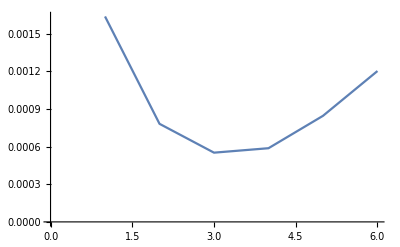

```mathematica
ListLinePlot[misfit4[0.5,1.5,0]]
```

```mathematica
d20=Table[misfit4[0.5,1.98,0],1000]
ζ20=N[Mean[Table[Abs[3-Position[d20[[x]],Min[d20[[x]]]][[1,1]]]/3,{x,100}]]]
```

{{0.00181217,0.000950133,0.000744831,0.000813092,0.0011315,0.00159396},{0.00181883,0.000926241,0.000720486,0.000794236,0.0011382,0.00159973},{0.00185767,0.00102292,0.00081474,0.000883589,0.00116981,0.00157599},{0.00252892,0.0014658,0.00106317,0.00101842,0.00117957,0.0014557},{0.00181441,0.000898935,0.000628774,0.000669678,0.000928039,0.00131508},{0.00179503,0.000983509,0.000818398,0.000920927,0.00128034,0.0017357},{0.00246727,0.00129425,0.000847097,0.000789238,0.000953706,0.0012674},{0.00234128,0.00131358,0.000953417,0.00094545,0.00114728,0.00149519},{0.00192092,0.00105613,0.000858848,0.000931273,0.00124507,0.00166971},{0.0011223,0.000657015,0.000795107,0.00107278,0.00165787,0.00231776},{0.0021151,0.00108721,0.000751105,0.000763278,0.00100973,0.0013933},{0.00227265,0.00125323,0.000956632,0.000973353,0.00124995,0.00168046},{0.00210699,0.00104322,0.000701054,0.000707916,0.000925741,0.00129924},{0.00194128,0.0010548,0.000812263,0.000878432,0.00114938,0.00155438},{0.00144609,0.000706332,0.000628107,0.000790583,0.00123335,0.00178774},{0.00199682,0.00104927,0.000782508,0.000832891,0.00110931,0.00152395},{0.0022984,0.00135602,0.00106369,0.00108383,0.0013057,0.00163848},{0.0023781,0.00132793,0.000942243,0.00090941,0.00107492,0.00140497},{0.00174937,0.000996432,0.000880772,0.00100079,0.00139263,0.00189306},{0.00287835,0.00173405,0.00125327,0.00115873,0.00121405,0.0014654},{0.00235339,0.00129742,0.000918047,0.00089615,0.00109363,0.00143013},{0.00199597,0.00111682,0.00085511,0.00090023,0.00116454,0.00156443},{0.00166243,0.00101648,0.000969851,0.00112809,0.00153341,0.00203555},{0.00244358,0.0014792,0.00117138,0.00117063,0.00141525,0.00180297},{0.00175026,0.000957897,0.000810651,0.00092236,0.00128344,0.00175821},{0.00148501,0.000733577,0.000619644,0.00076783,0.0011753,0.00170581},{0.00196492,0.0010799,0.000844405,0.000912273,0.00119582,0.00158906},{0.00169046,0.000901065,0.000732671,0.000813255,0.00112219,0.00156211},{0.0015377,0.000756876,0.000620288,0.000740463,0.00113131,0.00163008},{0.00220162,0.00123129,0.000930925,0.000951456,0.00116972,0.0015554},{0.00171743,0.00090865,0.00072299,0.000806185,0.00112144,0.0015484},{0.00205849,0.0010756,0.000776193,0.000782566,0.00102715,0.0013984},{0.00219687,0.00128382,0.00102041,0.00104133,0.00126654,0.00164805},{0.00189414,0.00100186,0.000761972,0.000803598,0.00108626,0.00150373},{0.00193717,0.00116624,0.000997915,0.00110936,0.00142916,0.0019054},{0.0024249,0.00132949,0.000921724,0.000871999,0.00104889,0.00140524},{0.0011252,0.000629892,0.00072095,0.000976327,0.00151765,0.00216864},{0.00113332,0.000612861,0.000708018,0.000943432,0.00147462,0.00208337},{0.00162561,0.000848998,0.000689178,0.000775011,0.00111412,0.00155855},{0.00206699,0.00115069,0.00089484,0.000948981,0.00122981,0.00167193},{0.00188499,0.000981822,0.000703145,0.000738739,0.000991827,0.00137342},{0.00209517,0.00109964,0.000762474,0.000787544,0.00100761,0.00139247},{0.00232325,0.00123661,0.0008802,0.000891723,0.00112685,0.00151285},{0.00325314,0.00198858,0.00142868,0.0013046,0.001352,0.00154156},{0.00190099,0.00105847,0.000851498,0.000909656,0.00119096,0.00161591},{0.00205008,0.00106856,0.000743148,0.000744346,0.000947032,0.00129917},{0.0026086,0.00157835,0.00121652,0.0012018,0.0014219,0.001806},{0.00133767,0.000703461,0.000674472,0.000841002,0.00129411,0.00181986},{0.00182461,0.000981883,0.000807474,0.000881958,0.0012173,0.00165628},{0.00213765,0.00118807,0.000885151,0.000885317,0.00110826,0.00146936},{0.00178151,0.000947179,0.000726138,0.000794615,0.00109919,0.00155494},{0.00185781,0.000937125,0.000682635,0.000727421,0.00100638,0.00142299},{0.00253496,0.00140979,0.000994698,0.000943099,0.00108301,0.00136026},{0.00205835,0.00107931,0.000761077,0.000781757,0.0010165,0.00140075},{0.00199061,0.00107896,0.000843009,0.000912707,0.00122696,0.00167701},{0.00174365,0.000871282,0.000659264,0.000738477,0.00106077,0.00149393},{0.00179679,0.00093728,0.000752185,0.000837161,0.00114836,0.00158108},{0.0015002,0.000786709,0.000695096,0.000838904,0.00125108,0.00177545},{0.00223499,0.00121244,0.000916282,0.000947136,0.00123491,0.00167605},{0.00202937,0.00113682,0.000875885,0.000910262,0.0011404,0.0015077},{0.00213094,0.00122882,0.000959689,0.00101191,0.00127959,0.00170253},{0.00171577,0.00089165,0.000727844,0.000820765,0.00115844,0.0016182},{0.0014025,0.000767932,0.000761138,0.000961326,0.00144171,0.00201319},{0.00166149,0.000941951,0.000888933,0.00106691,0.00152026,0.00209376},{0.00229629,0.00123169,0.000897545,0.000887546,0.00112221,0.00151341},{0.00206967,0.00120125,0.000995429,0.00106467,0.00138264,0.00180362},{0.00156819,0.000858048,0.000754078,0.000883181,0.00125345,0.00172451},{0.00152263,0.000913749,0.000893785,0.00107442,0.00153281,0.00207673},{0.00156668,0.000775648,0.000643891,0.000756542,0.00112156,0.00161409},{0.00180909,0.00102775,0.000855351,0.00096058,0.00128706,0.00176076},{0.00200474,0.00116022,0.000973752,0.00105198,0.00134204,0.00175516},{0.00182262,0.0010017,0.000835631,0.000913089,0.00125055,0.00170186},{0.00175105,0.000958979,0.000813457,0.000923388,0.00128067,0.00174938},{0.00150457,0.000863956,0.000856979,0.00103406,0.00149003,0.00203556},{0.00239453,0.00137688,0.000976219,0.000929736,0.00107918,0.00139502},{0.00162316,0.000873698,0.000737562,0.000850778,0.00121436,0.00167974},{0.00126532,0.00065774,0.00065002,0.000848162,0.00131997,0.00188295},{0.00214312,0.00119049,0.000936204,0.000984418,0.00127057,0.00168039},{0.00164715,0.000943405,0.000843949,0.00098725,0.0013638,0.00183908},{0.00195604,0.00108071,0.000830069,0.000884716,0.00117112,0.0015823},{0.00231083,0.00136273,0.00108368,0.00112186,0.00138101,0.00179557},{0.0015927,0.00100433,0.0010162,0.00120988,0.0016754,0.00224634},{0.00189552,0.00105083,0.000857896,0.000960069,0.00129592,0.001751},{0.00238198,0.00154134,0.00128895,0.00132892,0.0015885,0.00195068},{0.00187015,0.000932033,0.000683825,0.000733432,0.00103644,0.00146918},{0.00193986,0.00110532,0.000899721,0.000976839,0.0012854,0.00169796},{0.00184139,0.0010508,0.000896286,0.000986189,0.00132614,0.00179604},{0.00168334,0.000964739,0.000876274,0.00101735,0.00142411,0.00194294},{0.0020733,0.0011403,0.00088336,0.000936779,0.00123864,0.0016782},{0.00163069,0.000833234,0.00070335,0.000828632,0.00119603,0.00168814},{0.00181288,0.00101378,0.000852003,0.000962344,0.00132654,0.00181901},{0.00160087,0.00087754,0.00078742,0.000930511,0.00132133,0.00183278},{0.00155463,0.00078614,0.000644721,0.000761886,0.00113099,0.00162936},{0.00189999,0.00105434,0.000889269,0.000982803,0.00133083,0.0018078},{0.0015725,0.000790085,0.00063676,0.000740301,0.00109501,0.00157015},{0.00168334,0.000884941,0.000693459,0.000780601,0.0010991,0.0015285},{0.00221687,0.00133446,0.00109782,0.00115426,0.00145142,0.00190401},{0.00163911,0.000869953,0.000760418,0.000909885,0.00131959,0.00185961},{0.001807,0.000881777,0.000647054,0.000707842,0.00101403,0.00146197},{0.00150073,0.000765868,0.00069758,0.000859705,0.00130191,0.00184757},{0.0021488,0.0011575,0.000814957,0.00082903,0.00102137,0.00137799},{0.00198482,0.00108107,0.000812947,0.000854897,0.00112684,0.00154927},{0.0020124,0.00108725,0.000825227,0.000856438,0.00111628,0.001525},{0.00244569,0.00144321,0.00114084,0.00116644,0.00140731,0.00183138},{0.00174134,0.000856018,0.000622781,0.000686366,0.000988393,0.00144045},{0.00184344,0.000928698,0.000688613,0.000753884,0.00106839,0.00152647},{0.00196247,0.000987319,0.000687479,0.000719589,0.000990795,0.0013939},{0.00145626,0.000747493,0.000646591,0.000796494,0.00118455,0.00170223},{0.00161035,0.000870642,0.000800391,0.000943679,0.00136211,0.00187727},{0.0023594,0.00135504,0.00101053,0.000992244,0.0012127,0.00157639},{0.00206954,0.00116548,0.000896245,0.000943262,0.00121512,0.0016423},{0.00207966,0.00115293,0.000871769,0.000926021,0.00118538,0.00157915},{0.00193705,0.00104409,0.000817398,0.000874537,0.00117463,0.00160604},{0.00122991,0.000691301,0.000766158,0.00101087,0.00155951,0.0022033},{0.00129653,0.000693648,0.000720325,0.000925741,0.00142471,0.0020193},{0.00191404,0.00102454,0.000837765,0.000918942,0.00126129,0.00173943},{0.00221613,0.00124134,0.000902999,0.000910979,0.00109786,0.00145068},{0.00148219,0.000793455,0.000730921,0.000883172,0.00130484,0.00182077},{0.00158133,0.000843736,0.000778591,0.000943997,0.00137989,0.0019379},{0.00244198,0.00133555,0.000906787,0.000871645,0.00101713,0.00134043},{0.00137014,0.000914596,0.00101565,0.00126237,0.00176234,0.00232151},{0.00179662,0.00100558,0.000821894,0.000911473,0.00122501,0.00165686},{0.00199258,0.00103379,0.000745934,0.000775497,0.00104599,0.00145865},{0.00204482,0.00103533,0.000718261,0.000732229,0.000991395,0.00138361},{0.00196923,0.00110054,0.000873749,0.00093636,0.00122281,0.00166055},{0.00194124,0.00106194,0.000820713,0.000877552,0.00115941,0.0015753},{0.00146705,0.000825455,0.00081769,0.00100865,0.00146847,0.00203318},{0.00213912,0.00114966,0.000832795,0.000860697,0.00112053,0.00154784},{0.00225184,0.00134161,0.00106301,0.00110156,0.00134709,0.00175611},{0.0016991,0.000837096,0.000640383,0.000715082,0.0010522,0.00149043},{0.00203036,0.00104096,0.000696047,0.000705151,0.000897417,0.00123426},{0.00170233,0.000838712,0.000654413,0.000737237,0.00108513,0.00155403},{0.0017389,0.000986977,0.000846309,0.00096432,0.00133716,0.00181985},{0.00189689,0.00112131,0.000959965,0.00105946,0.00137591,0.0018235},{0.00147602,0.000902995,0.000895155,0.00108172,0.00152144,0.00207936},{0.00158902,0.000743299,0.000568537,0.000666454,0.00102226,0.00149886},{0.00264234,0.00165275,0.00132714,0.00131754,0.00150715,0.00180235},{0.00191971,0.00105923,0.000803948,0.0008519,0.00112043,0.00152428},{0.00153837,0.000830964,0.000737767,0.00088562,0.00128834,0.00178841},{0.0016563,0.000899758,0.000734335,0.000835865,0.00116119,0.00161021},{0.0016219,0.000895269,0.000825392,0.000978244,0.001409,0.00197315},{0.00188763,0.000990593,0.000733013,0.000784436,0.00104244,0.00143931},{0.00296636,0.00184319,0.00136987,0.00129421,0.00137558,0.00158989},{0.00172206,0.000923526,0.000748359,0.000860391,0.00119717,0.00164844},{0.00153484,0.000813504,0.000721989,0.000849944,0.00122906,0.00173748},{0.00144727,0.000705013,0.000579598,0.00069533,0.00106272,0.00154958},{0.00118888,0.000586398,0.000582818,0.000773266,0.00122123,0.00177969},{0.0014296,0.000741712,0.000658297,0.000797859,0.00118885,0.00168497},{0.00135015,0.00063378,0.000547959,0.000693402,0.00108818,0.00158838},{0.00219512,0.0012856,0.00100514,0.00103552,0.00125266,0.00161685},{0.00191113,0.00106686,0.000844609,0.00090014,0.00117387,0.00161273},{0.00240121,0.00127555,0.000833189,0.000775182,0.000916173,0.00122797},{0.00207907,0.00115305,0.000857903,0.000886416,0.00110273,0.00148502},{0.00185853,0.000980982,0.000723911,0.000773057,0.00103264,0.0014333},{0.00166348,0.000857209,0.000729852,0.000869776,0.00127142,0.00180846},{0.00179922,0.000969876,0.000796617,0.000903253,0.00124783,0.00170974},{0.00244496,0.00133131,0.000947648,0.000916671,0.00111631,0.00146535},{0.0018279,0.000962069,0.000727692,0.000794307,0.00109285,0.00151941},{0.00278466,0.00163066,0.00117064,0.00110206,0.00122959,0.00149607},{0.00229655,0.00138779,0.00112016,0.00113803,0.00137485,0.00176079},{0.00232959,0.00135395,0.00102985,0.00104396,0.00126606,0.00165405},{0.00174065,0.00090689,0.000697674,0.000795141,0.00112666,0.00160054},{0.00176138,0.000981099,0.00082105,0.000929019,0.00128249,0.00174365},{0.00152107,0.000941127,0.000926357,0.00110661,0.00154268,0.0020582},{0.00172125,0.000848573,0.000663884,0.000751386,0.00108722,0.00155131},{0.00180072,0.000950673,0.000749684,0.000832129,0.0011597,0.00159916},{0.00184029,0.000999818,0.000778613,0.000838577,0.00112132,0.00153653},{0.00235786,0.00133433,0.000974293,0.000953012,0.00113691,0.00146448},{0.00126703,0.000686573,0.000696365,0.000913221,0.00137548,0.00193967},{0.00194117,0.00114798,0.000964577,0.00105088,0.00137012,0.00179793},{0.00169623,0.000930348,0.000790567,0.00091165,0.00127552,0.00175015},{0.00164195,0.000825766,0.000623566,0.000692097,0.00098877,0.00142524},{0.00238647,0.00141862,0.00106519,0.0010502,0.00122451,0.00153178},{0.00202866,0.00115129,0.000917897,0.000980859,0.00125676,0.00165674},{0.0016955,0.000894569,0.000716231,0.000812964,0.00116372,0.00162005},{0.00152638,0.000866634,0.000807985,0.000969189,0.00138829,0.00191477},{0.00176471,0.0010055,0.000875707,0.000998252,0.00136092,0.00185889},{0.00160242,0.000909494,0.000815756,0.000953737,0.00132959,0.00180758},{0.00192855,0.000991441,0.000731548,0.000783706,0.00107381,0.00150462},{0.00190529,0.00103217,0.000823605,0.000907809,0.00125104,0.00172781},{0.00145973,0.000734168,0.00061491,0.000759857,0.00114974,0.00166389},{0.00211994,0.00123131,0.00101773,0.00109302,0.00140687,0.00184418},{0.00154536,0.000776493,0.00064952,0.000788155,0.00118011,0.00169283},{0.00218987,0.00123242,0.000965052,0.00100008,0.00127674,0.00169712},{0.00191754,0.00105225,0.000841554,0.000915388,0.00121438,0.00164386},{0.00202926,0.00107065,0.000767231,0.000794664,0.0010135,0.00137116},{0.0022548,0.00126344,0.000957326,0.000992412,0.00124926,0.00167421},{0.00168118,0.000814834,0.000634055,0.000740154,0.00112393,0.00164926},{0.00224186,0.00129388,0.000964062,0.000976011,0.00117177,0.00153618},{0.00157597,0.000792294,0.00064082,0.000755105,0.00112723,0.00160062},{0.00193491,0.00103683,0.000788706,0.000854639,0.00113637,0.00155435},{0.00189772,0.00105707,0.000877159,0.000977683,0.00134913,0.00182262},{0.00145887,0.000747628,0.000663795,0.000816422,0.00124184,0.00176154},{0.00160721,0.00083777,0.000668846,0.0007658,0.00108803,0.00152285},{0.00164822,0.000761565,0.000537317,0.000608955,0.000910497,0.00133541},{0.00167418,0.000944637,0.000821894,0.00095362,0.00131837,0.00178551},{0.00255741,0.00154966,0.00120178,0.00118426,0.00135979,0.00169587},{0.00208081,0.00109867,0.000791557,0.000809235,0.00107146,0.0014871},{0.00255506,0.00152458,0.00115735,0.00114883,0.0013405,0.00173809},{0.00191498,0.000930865,0.000655468,0.000707614,0.000996376,0.00141756},{0.00263444,0.00153226,0.00112764,0.00108851,0.00125656,0.0016055},{0.0013475,0.000782263,0.000801237,0.000997668,0.00146097,0.00202423},{0.00190421,0.00108237,0.000960181,0.0010704,0.00147441,0.001977},{0.00163114,0.000817563,0.000624451,0.000700957,0.00100777,0.00144702},{0.00261854,0.00160967,0.00126646,0.00125242,0.00144538,0.0018103},{0.00243536,0.00137611,0.00100172,0.000955571,0.00113216,0.0014652},{0.00220706,0.00117943,0.000850166,0.000862824,0.00109241,0.00149493},{0.00158232,0.000869498,0.000797011,0.000945277,0.0013842,0.00192573},{0.00192169,0.00106774,0.000902363,0.00101062,0.0013949,0.00193056},{0.0018856,0.00104635,0.000848692,0.000926816,0.00125779,0.0016874},{0.00209114,0.00111144,0.00079867,0.00084505,0.00110601,0.00152565},{0.00209853,0.00117779,0.000936759,0.000994807,0.00129644,0.00173113},{0.00174676,0.000959713,0.000777069,0.000868286,0.0012099,0.00168484},{0.00200975,0.00103366,0.000718676,0.000735958,0.000987324,0.00138389},{0.00127831,0.00065779,0.00068289,0.000895666,0.00139602,0.0019868},{0.00282861,0.00173615,0.00128627,0.001228,0.00135431,0.00165681},{0.00201132,0.00109658,0.000849541,0.000904994,0.00118513,0.00161633},{0.00217948,0.00129007,0.00100963,0.00102749,0.00124731,0.00160451},{0.00216574,0.00118965,0.000884557,0.000905893,0.00113978,0.00156114},{0.00170357,0.00095068,0.000872789,0.00100934,0.00143045,0.00197301},{0.00176418,0.000948838,0.000799424,0.000911015,0.00124552,0.00168502},{0.00218622,0.00120433,0.000941758,0.00097646,0.00126606,0.00169238},{0.00187999,0.00104149,0.000812414,0.000879795,0.00116789,0.0016034},{0.00226168,0.00129296,0.000997958,0.00101284,0.00125065,0.00164948},{0.00188541,0.00100728,0.000766356,0.00083678,0.00113776,0.00158368},{0.00217362,0.00116201,0.000865057,0.000902941,0.00117171,0.00158865},{0.00220957,0.00115906,0.000803086,0.000789312,0.00101231,0.001364},{0.00173753,0.000947261,0.000805853,0.000919393,0.00127956,0.00175016},{0.0015765,0.000874781,0.000819303,0.000963168,0.00138157,0.00188592},{0.00160931,0.000870357,0.000769076,0.000921138,0.00133247,0.0018428},{0.00130548,0.000733953,0.000758108,0.000962638,0.00147371,0.00205692},{0.00204149,0.00116717,0.000906488,0.000937103,0.00119451,0.00159647},{0.00215286,0.00120736,0.000892198,0.000897784,0.00112192,0.00150134},{0.00156065,0.000832406,0.000741048,0.000885469,0.00127145,0.00176314},{0.00152331,0.000771356,0.000642405,0.000771806,0.00115282,0.00166237},{0.00225005,0.00118703,0.000824739,0.000816662,0.0010135,0.00138577},{0.00221821,0.00113275,0.000741504,0.000712546,0.000890701,0.0012267},{0.00145361,0.000793993,0.000749915,0.000924115,0.00138189,0.00193507},{0.00214962,0.00120639,0.000935621,0.00098597,0.00127653,0.00172999},{0.00153892,0.000892182,0.000843599,0.00101481,0.00144542,0.00200328},{0.00236471,0.00128489,0.000887522,0.000847315,0.00100504,0.00133951},{0.00177056,0.000944625,0.00076711,0.000846058,0.00116313,0.00157789},{0.00179137,0.000929388,0.000709691,0.000786995,0.00109607,0.0015424},{0.00212002,0.00117123,0.000869762,0.000903375,0.00114521,0.00154666},{0.00214425,0.00118939,0.000911047,0.000941932,0.00122508,0.00164229},{0.00133141,0.00068426,0.000652786,0.000832499,0.00127198,0.00181036},{0.00147259,0.000778199,0.000701692,0.00084352,0.00124172,0.0017523},{0.00192965,0.00115966,0.000972864,0.00106021,0.00138185,0.0018117},{0.00207949,0.00108481,0.000775484,0.000792597,0.00102048,0.00140388},{0.00162569,0.000799441,0.000607292,0.000697372,0.00101929,0.00146944},{0.0016133,0.000807303,0.000645655,0.000756065,0.00112962,0.00161519},{0.00147054,0.000790568,0.000770419,0.000951917,0.00140292,0.00192467},{0.00185394,0.000980955,0.000769953,0.0008471,0.0011648,0.00161755},{0.00243937,0.00134835,0.000968944,0.00095585,0.00116413,0.00153419},{0.00180201,0.000914673,0.000676883,0.00073134,0.00102278,0.00146264},{0.00151623,0.000825529,0.000724796,0.000872868,0.00126617,0.00179175},{0.00123201,0.000648549,0.00066289,0.000873655,0.00137611,0.00199482},{0.00206041,0.00120404,0.000988576,0.00106063,0.00135096,0.00173931},{0.00213962,0.00122148,0.000940545,0.000972959,0.00120833,0.00157947},{0.00167163,0.000841288,0.000663026,0.000764322,0.0011245,0.00160454},{0.00215467,0.00115305,0.000848682,0.000859521,0.0010943,0.00147699},{0.00192012,0.00111945,0.000939999,0.00102768,0.00133153,0.00178203},{0.00151599,0.000761398,0.000655447,0.000792414,0.00117535,0.00166576},{0.0023304,0.00140579,0.00108527,0.0010944,0.00131531,0.0017125},{0.00279321,0.00174062,0.00128604,0.00121866,0.00133238,0.0015965},{0.00179676,0.000968197,0.000804506,0.000902051,0.00127533,0.00176654},{0.00203187,0.00105193,0.000739002,0.000758204,0.000988413,0.00136829},{0.00124308,0.000714355,0.000784106,0.00102587,0.00155052,0.00214985},{0.00221407,0.00119777,0.000879704,0.000889945,0.001128,0.00153234},{0.00233123,0.00138966,0.00111501,0.00114787,0.00140248,0.00177636},{0.00179238,0.00100166,0.000867608,0.000982057,0.00135949,0.00183217},{0.0013672,0.000821781,0.00086648,0.00109439,0.00159379,0.00219755},{0.0017976,0.000949049,0.000727942,0.000805649,0.00109886,0.00154418},{0.00197063,0.00108733,0.00087731,0.000949676,0.00126594,0.0016982},{0.00213438,0.00112312,0.000784808,0.000783046,0.000997071,0.00135108},{0.00192428,0.000971101,0.000671744,0.000709285,0.000961685,0.00139305},{0.00147126,0.00071882,0.000604143,0.000730059,0.00109988,0.00158386},{0.00186811,0.000995862,0.000782214,0.000852049,0.0011603,0.00160285},{0.00142382,0.000751503,0.000723884,0.000898442,0.00135802,0.00191601},{0.0026372,0.0016787,0.00132662,0.00131199,0.00147567,0.00179207},{0.00238783,0.00141501,0.00112223,0.00115183,0.00140653,0.00180396},{0.00163857,0.000840055,0.000688707,0.000786139,0.0011294,0.00161298},{0.00149498,0.000818077,0.000790514,0.000959822,0.00142121,0.00198079},{0.00155438,0.000829545,0.000752153,0.000892236,0.00131854,0.00183897},{0.00226333,0.00131346,0.00101691,0.00104558,0.0012834,0.00166958},{0.00189772,0.000960006,0.000697337,0.000745745,0.0010282,0.00144932},{0.001999,0.00105948,0.00078718,0.00080915,0.00106978,0.00144748},{0.00191397,0.00103919,0.000851066,0.000923384,0.0012492,0.00168633},{0.00143119,0.000802023,0.000791039,0.000967555,0.00142741,0.00198422},{0.00190223,0.00100223,0.000764671,0.000829186,0.00111859,0.00153484},{0.00154512,0.000857118,0.00078976,0.000947983,0.00137799,0.00193233},{0.0021524,0.00120386,0.000900917,0.000909267,0.00114887,0.00150199},{0.00201273,0.0010677,0.00082182,0.000877912,0.00117917,0.00161245},{0.00152976,0.000882708,0.000853966,0.00104199,0.0014968,0.00205544},{0.00216255,0.0011895,0.000864579,0.000873553,0.00109746,0.00146497},{0.00167694,0.000842217,0.000660725,0.000734683,0.0010566,0.00150078},{0.00208724,0.00118632,0.000945943,0.00100084,0.00127936,0.0017361},{0.00182671,0.000928092,0.000727252,0.000827358,0.00115579,0.00162331},{0.00133491,0.000747217,0.000755505,0.000948491,0.00141866,0.00196944},{0.00248059,0.00139608,0.00100814,0.00097347,0.00114165,0.00148949},{0.00238806,0.00132504,0.000955724,0.000938541,0.00114112,0.00152007},{0.0016791,0.000890035,0.000705218,0.00080349,0.00112706,0.00158329},{0.00197698,0.0010583,0.000832302,0.000878582,0.00116456,0.00157174},{0.00241078,0.0012869,0.000851769,0.00081725,0.00100055,0.00134989},{0.00193013,0.00096833,0.000704141,0.000744801,0.00100375,0.00139615},{0.00160469,0.000917303,0.000882077,0.00105226,0.00152259,0.00209325},{0.0015359,0.000922451,0.000899098,0.00109342,0.00154356,0.00209583},{0.00179773,0.000992867,0.000856888,0.00097213,0.00136345,0.00184867},{0.00150257,0.000775032,0.000658915,0.000798314,0.00115993,0.00164217},{0.00151729,0.000796537,0.000728817,0.000882337,0.00130471,0.00182717},{0.00174949,0.000912583,0.000752314,0.000851638,0.00121898,0.00169959},{0.00190712,0.00100639,0.000784126,0.000847785,0.00115995,0.00160532},{0.00236007,0.00136257,0.00100058,0.00097372,0.00113318,0.00145762},{0.00183681,0.000918216,0.000649581,0.000690082,0.000964171,0.00139597},{0.00172367,0.000881645,0.000689159,0.0007677,0.00106891,0.0014956},{0.00204577,0.00108172,0.000773381,0.000805926,0.00105624,0.00143211},{0.00247702,0.00146842,0.00112769,0.00112178,0.00132652,0.00167337},{0.00204147,0.0011701,0.000963144,0.00103743,0.00135286,0.00178984},{0.00202612,0.0011215,0.000865354,0.00090979,0.00116782,0.00156849},{0.00152631,0.000818193,0.00071057,0.00084762,0.00124033,0.00172905},{0.00146341,0.000747076,0.00064587,0.000782303,0.00116286,0.00166343},{0.00202216,0.00110842,0.000886726,0.000958124,0.00127543,0.00172488},{0.00243905,0.00132615,0.000961871,0.000942413,0.00114895,0.00153471},{0.00146771,0.000728748,0.000625326,0.000765977,0.00114885,0.00163609},{0.00135775,0.000685094,0.000650463,0.000825281,0.00129849,0.00185856},{0.00178512,0.00100083,0.000859091,0.000970686,0.00131028,0.00177723},{0.00197302,0.00101991,0.000746284,0.00077784,0.0010565,0.00148641},{0.00143544,0.000803819,0.000765259,0.000932371,0.00135051,0.00189042},{0.00274348,0.00159161,0.00115848,0.00111214,0.00127164,0.00160671},{0.00287002,0.00172626,0.00125864,0.00119584,0.00129939,0.00158},{0.00118615,0.000632456,0.000678282,0.000902172,0.00139992,0.00199159},{0.00203367,0.00113805,0.000893828,0.000948056,0.00123436,0.00168641},{0.00245448,0.00136053,0.00100078,0.000990935,0.00122267,0.00159479},{0.00251587,0.0014197,0.00101846,0.000982927,0.00116385,0.00151342},{0.00205977,0.00109968,0.00080431,0.00083405,0.0010695,0.00147143},{0.00184282,0.000956031,0.000742143,0.000799111,0.00111662,0.00155629},{0.00196087,0.00109444,0.000887698,0.000956206,0.00123937,0.00162789},{0.00171658,0.000927947,0.000769273,0.000858377,0.00121982,0.00169311},{0.00223594,0.00128765,0.000972331,0.000979034,0.00120205,0.00156582},{0.00190608,0.00112238,0.000956298,0.00105323,0.00138584,0.00183604},{0.00187175,0.00105874,0.000882786,0.000963869,0.00128994,0.00174195},{0.00211501,0.00116,0.000888845,0.000938025,0.0012151,0.00162603},{0.00194168,0.00108271,0.000852401,0.000904018,0.00120524,0.00163477},{0.001313,0.000632217,0.000579227,0.000758897,0.00119991,0.00173868},{0.00156382,0.00084446,0.000747657,0.000896679,0.00129838,0.00182492},{0.00170651,0.000890559,0.000738673,0.000850398,0.00121591,0.0016944},{0.00225081,0.00120092,0.000826288,0.000793023,0.000982452,0.00131059},{0.00171394,0.000872325,0.000687872,0.000794924,0.00114331,0.00161641},{0.00239446,0.0013671,0.000987095,0.000953689,0.00113176,0.00147071},{0.00148086,0.000822988,0.000727201,0.000857208,0.00121816,0.00168789},{0.00157508,0.000837228,0.000717791,0.000853113,0.00125916,0.00177102},{0.00171129,0.000909039,0.000784924,0.000912674,0.00129682,0.00179738},{0.00245216,0.00142791,0.00106911,0.00103723,0.00120419,0.00152156},{0.00154415,0.000790543,0.000705448,0.000860841,0.00128477,0.00182317},{0.00251165,0.00148211,0.00110369,0.00108279,0.00123496,0.00154216},{0.00188632,0.000981693,0.000727618,0.000771837,0.0010439,0.0014561},{0.00172694,0.00101656,0.000925783,0.00107479,0.00148759,0.00200607},{0.00223448,0.00126785,0.00100019,0.00104447,0.00131893,0.00173294},{0.00227209,0.00126181,0.000937378,0.000939722,0.00115813,0.00150362},{0.00175016,0.00095917,0.000801193,0.000907119,0.00123467,0.00169138},{0.00192211,0.000971415,0.000680529,0.000714402,0.000982076,0.00138857},{0.00216048,0.0012948,0.00107358,0.0011311,0.00142926,0.00183595},{0.00225918,0.00151674,0.00132135,0.00138335,0.00163642,0.002031},{0.00206644,0.00120162,0.000930167,0.000971942,0.00123154,0.00163718},{0.00231774,0.00126193,0.000922051,0.000924691,0.00116986,0.00156847},{0.00162938,0.000840153,0.000712176,0.000819553,0.0011919,0.00166945},{0.00201997,0.001017,0.000716398,0.000743092,0.00100579,0.00143373},{0.00182432,0.000976877,0.000814412,0.000904192,0.00124273,0.00169446},{0.00231228,0.00132472,0.00100857,0.00101512,0.001256,0.00160198},{0.00175184,0.000944144,0.000773619,0.00086157,0.00118747,0.00161361},{0.00195285,0.000957875,0.000637325,0.000645645,0.000881564,0.00127565},{0.00162415,0.000854669,0.000724428,0.000847037,0.00122783,0.00172477},{0.00218793,0.00120625,0.000852982,0.000851574,0.00105526,0.00142366},{0.00168372,0.00089614,0.000750207,0.000851052,0.00120465,0.00168751},{0.00196176,0.00103965,0.000771422,0.000810495,0.00106831,0.00148321},{0.00168793,0.000897539,0.000749046,0.000846991,0.00116928,0.00162255},{0.00235024,0.00132956,0.000969776,0.000978181,0.00117257,0.00153542},{0.00186971,0.000986554,0.000749709,0.000800227,0.00110159,0.0015295},{0.00188138,0.00105283,0.000859281,0.000941196,0.00127378,0.00173689},{0.0012218,0.0007244,0.00079554,0.00100577,0.00149699,0.00207618},{0.00203223,0.00105071,0.000748191,0.000779352,0.00105278,0.00145026},{0.00196154,0.0011647,0.000971305,0.00103917,0.00133297,0.00173428},{0.00170524,0.000909375,0.000725771,0.000806838,0.00111608,0.00155016},{0.00214988,0.00109473,0.000769991,0.00078124,0.0010618,0.00147641},{0.00140106,0.000795194,0.000829798,0.00103695,0.00153268,0.00213794},{0.00246066,0.00138732,0.00102092,0.00101399,0.00120665,0.00157813},{0.00222441,0.00121453,0.000865682,0.000844255,0.00101919,0.00135985},{0.00218026,0.00119576,0.000922971,0.0009592,0.00124642,0.00169252},{0.00211641,0.00119835,0.000928599,0.000976239,0.00122205,0.00162012},{0.00235027,0.00133008,0.00098331,0.000990719,0.00121588,0.00159506},{0.00186249,0.00107417,0.000941533,0.00105625,0.00143129,0.00194602},{0.00162191,0.000893101,0.000769522,0.000898865,0.00126372,0.00173634},{0.00211583,0.00113458,0.000841972,0.00086622,0.0011331,0.00154906},{0.00241123,0.00140094,0.0010426,0.00101736,0.00121423,0.00155788},{0.00162164,0.00106443,0.00106696,0.00125339,0.00171959,0.00226122},{0.0018751,0.000962816,0.000724064,0.0007843,0.00107573,0.00147197},{0.00184449,0.00106815,0.000947199,0.00107091,0.0014685,0.00194665},{0.00181473,0.000906918,0.000658422,0.000720396,0.00102845,0.001481},{0.00152288,0.000872865,0.000840604,0.000993136,0.00141824,0.00193959},{0.00151805,0.00080043,0.000684194,0.000813384,0.00118724,0.00167009},{0.00172935,0.000938498,0.000809867,0.000940139,0.0013247,0.00183651},{0.0013776,0.000684758,0.000588953,0.00072267,0.00109607,0.00157318},{0.00179764,0.000960683,0.000798333,0.000888445,0.00124099,0.00169758},{0.00127821,0.00068377,0.000673528,0.000875289,0.00131004,0.00185518},{0.0016833,0.000952346,0.000814316,0.000932394,0.00128396,0.00178479},{0.001576,0.000897043,0.000815387,0.000957276,0.00135532,0.00186095},{0.00242591,0.00132818,0.000943925,0.000933122,0.00114813,0.00155404},{0.00151575,0.000819777,0.000782385,0.000962427,0.00144934,0.00202023},{0.00173867,0.000867753,0.000650068,0.000720923,0.00103037,0.00146647},{0.00183424,0.00104184,0.000862421,0.000937472,0.00124081,0.00166247},{0.00183737,0.00102172,0.000834226,0.000914813,0.00123377,0.00167167},{0.00172267,0.00103909,0.000980109,0.00112988,0.00156223,0.00212035},{0.00190237,0.000999349,0.000745538,0.000802596,0.00107027,0.00145098},{0.00161897,0.000811164,0.00068019,0.000794436,0.00115697,0.00162973},{0.00179349,0.000995594,0.000835874,0.00092076,0.00125413,0.00169186},{0.0016441,0.000873662,0.000713876,0.000812304,0.00116756,0.00165097},{0.00243962,0.00146447,0.00112555,0.00112402,0.00133393,0.00170124},{0.00187068,0.00110337,0.000951434,0.00104941,0.00141785,0.00187311},{0.00211186,0.0012259,0.00100846,0.00105523,0.00135232,0.00178752},{0.0023851,0.00146276,0.00120617,0.00126416,0.00157035,0.00201524},{0.00151051,0.000916314,0.000927281,0.00114819,0.00164612,0.0022423},{0.00226344,0.00128449,0.000962351,0.000966581,0.00118397,0.00154184},{0.00159292,0.000829159,0.000702356,0.00081442,0.00119746,0.0016989},{0.00152978,0.000686543,0.000504542,0.00059095,0.000927337,0.00137472},{0.00209489,0.00117193,0.000940545,0.00100362,0.00134576,0.00180273},{0.00223317,0.00126497,0.000935887,0.000925914,0.00112389,0.00146286},{0.00136419,0.000709048,0.000646518,0.0008136,0.00123029,0.00176401},{0.00177375,0.000897926,0.000732663,0.000824149,0.00120466,0.00170281},{0.0020189,0.00108875,0.000811251,0.000860658,0.00112052,0.0015538},{0.00185343,0.000976981,0.000751214,0.000823917,0.00112314,0.0015634},{0.0014713,0.000887991,0.000931274,0.00115724,0.00165889,0.00225722},{0.00244986,0.00146995,0.00112219,0.00110559,0.00128389,0.00163534},{0.00133811,0.000794808,0.000834101,0.00104138,0.00152616,0.0020981},{0.00181648,0.00105352,0.000927312,0.00104661,0.00143262,0.00193344},{0.00126634,0.000783932,0.000853444,0.00109816,0.00158644,0.00217473},{0.00181285,0.000984032,0.000783949,0.000880131,0.00119232,0.00163708},{0.00177489,0.000923513,0.00073286,0.000829206,0.00118218,0.00167355},{0.00207785,0.0011133,0.000836644,0.000854379,0.00111644,0.00151477},{0.00160998,0.000858393,0.0007201,0.000828617,0.00119233,0.0016502},{0.00205495,0.00112253,0.000850132,0.000897797,0.00118037,0.0015966},{0.00218304,0.00132716,0.00108242,0.00112085,0.00137589,0.00177794},{0.00206955,0.00110635,0.000801018,0.000808746,0.00101388,0.0013659},{0.00184789,0.00101592,0.000841993,0.000938666,0.00127925,0.00174038},{0.00163123,0.000893228,0.000761196,0.000877191,0.00123347,0.00168104},{0.00132887,0.00067887,0.00063153,0.000814894,0.00125424,0.0017916},{0.0015691,0.00085633,0.000764148,0.000896015,0.00129126,0.00177926},{0.00224897,0.0012537,0.000949715,0.000975128,0.00121219,0.00162083},{0.00199086,0.00108388,0.000852989,0.000915325,0.00120229,0.00163491},{0.00227865,0.00125462,0.000906792,0.000917529,0.00113353,0.00148711},{0.0017839,0.000993651,0.000865457,0.000976821,0.00136798,0.00188364},{0.00203747,0.00120502,0.00102541,0.0011001,0.00142447,0.00184465},{0.00170942,0.000869431,0.000691662,0.000783869,0.00110391,0.00155008},{0.00227474,0.00127151,0.000921036,0.000924845,0.00115621,0.00152268},{0.00224276,0.00120679,0.000861252,0.000865792,0.00107874,0.00144364},{0.00204131,0.00115473,0.000957048,0.00105047,0.00141319,0.00188066},{0.00148542,0.000848745,0.000820177,0.000988389,0.00139798,0.00193349},{0.00132517,0.000728661,0.000746078,0.000940474,0.0013955,0.00193358},{0.00185016,0.000968197,0.000745161,0.000809861,0.00112711,0.0015576},{0.0015716,0.000870737,0.00078047,0.000920779,0.00129626,0.00178584},{0.00182998,0.00101536,0.000816748,0.000893876,0.00119174,0.00160356},{0.00201116,0.00105041,0.000771559,0.000801411,0.00107265,0.001499},{0.00199558,0.00104875,0.000779246,0.000813535,0.0010573,0.00147851},{0.00209671,0.00116385,0.000843099,0.000863334,0.00105814,0.00142005},{0.00193837,0.000965688,0.000658067,0.000679495,0.000918469,0.00130958},{0.00222901,0.00118677,0.000859752,0.000881448,0.00114361,0.00155205},{0.00182265,0.000964058,0.000746268,0.000820311,0.00113046,0.00157239},{0.0011102,0.000606544,0.00070841,0.000963695,0.00150583,0.00212724},{0.0018883,0.00114161,0.000970818,0.00106928,0.00136194,0.0017927},{0.00211189,0.00129134,0.00108983,0.001154,0.00143338,0.00182621},{0.00167747,0.000929459,0.0008268,0.000970176,0.00137105,0.00189696},{0.0020296,0.00113301,0.000868362,0.000907262,0.00116173,0.00154722},{0.00124558,0.000616939,0.000612429,0.000806696,0.00128373,0.00184307},{0.00217966,0.00116245,0.000800094,0.000795487,0.000981233,0.00132255},{0.00186165,0.000986861,0.00078351,0.000858889,0.00118509,0.00164355},{0.00208974,0.00109169,0.000771129,0.00079349,0.00103378,0.0014414},{0.00180142,0.000913516,0.000678055,0.000734267,0.00104003,0.00147891},{0.00169042,0.000902867,0.000723386,0.000804731,0.00111015,0.00154634},{0.00215225,0.00124752,0.000999404,0.00104032,0.00131119,0.00171921},{0.00163891,0.000830052,0.000692426,0.000807086,0.00119524,0.00169373},{0.00214193,0.00117979,0.000861167,0.000879442,0.00111313,0.001505},{0.00184292,0.000986838,0.000821355,0.000920043,0.00128244,0.00175292},{0.0019671,0.00108338,0.0008458,0.000884091,0.00117713,0.0016097},{0.00204,0.00113443,0.000896119,0.000954563,0.00123687,0.0016503},{0.00178848,0.00100559,0.000849397,0.000961444,0.00132597,0.00180302},{0.00184786,0.00099019,0.00076174,0.00081857,0.00107765,0.0014609},{0.00192735,0.0010047,0.000737293,0.000768463,0.00103376,0.00141211},{0.00183797,0.000930017,0.000699126,0.00076809,0.00108121,0.00153352},{0.00211339,0.00117329,0.000895332,0.000941224,0.00123289,0.00167035},{0.00196928,0.000988242,0.000683953,0.00070859,0.000922929,0.00128848},{0.00123163,0.000692806,0.000742672,0.000980925,0.00150683,0.00211905},{0.00184497,0.00101261,0.000823053,0.000915312,0.00123205,0.00166498},{0.00172016,0.000899465,0.000698061,0.00077247,0.00108622,0.00154299},{0.00174801,0.00086971,0.000676282,0.000766895,0.00112111,0.0015858},{0.0020725,0.00119772,0.000931984,0.000968609,0.0012144,0.00161494},{0.00169068,0.000912565,0.000744998,0.000847923,0.00118259,0.00161503},{0.00162338,0.00101044,0.00104146,0.00124285,0.00173576,0.00229026},{0.00147179,0.000774709,0.0007267,0.000902644,0.00134707,0.00191434},{0.0021179,0.0011722,0.000891527,0.000927903,0.00118368,0.0015946},{0.00194358,0.00104095,0.000811217,0.000859351,0.0011508,0.00156743},{0.0016938,0.000939064,0.000824054,0.000950467,0.00134475,0.00185019},{0.00192892,0.00103779,0.000807418,0.000878844,0.00120597,0.00164141},{0.00209388,0.00112587,0.000850608,0.000884064,0.00116793,0.00159964},{0.00199425,0.00108962,0.000892671,0.000971302,0.00131324,0.00175454},{0.00239186,0.00140344,0.00103897,0.00102866,0.00119895,0.00149754},{0.00157287,0.000898343,0.00084741,0.00100164,0.00141502,0.00191718},{0.00211891,0.00115855,0.000861777,0.00089342,0.00113741,0.00154369},{0.00188561,0.00102922,0.000852795,0.000938054,0.00130461,0.00177766},{0.0021689,0.00118532,0.000882484,0.000896057,0.00113775,0.001523},{0.00170448,0.000976752,0.000883753,0.00101176,0.00140587,0.00189153},{0.00189325,0.00101779,0.000803698,0.00087896,0.00120027,0.00164775},{0.00188955,0.00102879,0.000801222,0.000855276,0.00113966,0.00156006},{0.00167327,0.000810938,0.000638768,0.000749568,0.0011333,0.00165241},{0.00196632,0.00109137,0.000842557,0.000901011,0.00115818,0.00157793},{0.00198837,0.00116908,0.000964703,0.00103252,0.00132663,0.00173786},{0.00206361,0.000995416,0.00066341,0.000675904,0.000926775,0.00132217},{0.00186968,0.00103464,0.000870386,0.000971192,0.0013191,0.0017473},{0.00195876,0.000986218,0.000696519,0.000731864,0.00100368,0.00139192},{0.00217412,0.00127097,0.00101305,0.00103722,0.00130363,0.00168722},{0.00170274,0.000994466,0.000874994,0.00099558,0.00137312,0.00186002},{0.00173011,0.000924824,0.000745479,0.000819525,0.00114361,0.00158475},{0.0023063,0.00142032,0.00117001,0.00120099,0.00144941,0.00186641},{0.00208951,0.00118607,0.000948607,0.00100347,0.001297,0.00173299},{0.00204065,0.00121963,0.0010106,0.00107139,0.00134189,0.00174853},{0.00215359,0.00124247,0.000977104,0.00102064,0.0013039,0.00172065},{0.00167772,0.000936993,0.000828736,0.000952876,0.00134473,0.00187648},{0.00246792,0.0013937,0.000997539,0.000957346,0.00114639,0.00148225},{0.00241767,0.00134851,0.00092881,0.000871672,0.00100116,0.00129159},{0.00199079,0.00111656,0.000898068,0.00096509,0.00124288,0.00166033},{0.00202651,0.00101209,0.000676341,0.000671364,0.000887439,0.0012558},{0.00172933,0.000878127,0.000712561,0.000809207,0.00118629,0.0017175},{0.00200447,0.00113164,0.000885914,0.000942069,0.00120946,0.00161127},{0.00217611,0.00118153,0.000885166,0.000902685,0.00114298,0.001503},{0.00201837,0.00116492,0.000966823,0.00105602,0.00139064,0.00184391},{0.00216733,0.00119874,0.000893533,0.000927607,0.00119135,0.00158159},{0.00155721,0.000756343,0.000612963,0.00073469,0.00111235,0.00162196},{0.00164441,0.000899531,0.000790994,0.000895692,0.00126485,0.00173546},{0.00194697,0.00107671,0.000891233,0.00096219,0.00128627,0.00174506},{0.00187346,0.00103586,0.000828723,0.000895264,0.00118685,0.00161705},{0.00260943,0.0014374,0.000973936,0.000894523,0.00101761,0.00132668},{0.00219112,0.0012367,0.000919898,0.000940785,0.00116772,0.00154176},{0.00237609,0.0013293,0.000970262,0.000946999,0.00112571,0.00146401},{0.00194508,0.00102575,0.000777449,0.00083793,0.00111144,0.00152332},{0.00151705,0.000935127,0.000927166,0.00111971,0.00157492,0.00212238},{0.00229595,0.00132111,0.00102043,0.00105099,0.00130559,0.00170266},{0.00219334,0.00133993,0.00111837,0.00121286,0.00152765,0.00199297},{0.00214066,0.00120698,0.000940618,0.000979445,0.00124539,0.00163596},{0.00213359,0.00123401,0.000924248,0.000942562,0.00113505,0.00148545},{0.00231005,0.00122255,0.000831163,0.000807786,0.00101588,0.00140086},{0.00177536,0.00108131,0.00102752,0.00120432,0.00165942,0.00221787},{0.00204657,0.00105201,0.000741916,0.0007649,0.00102454,0.00144225},{0.00206488,0.0010731,0.000781818,0.000811436,0.00106653,0.00143163},{0.0015881,0.000832649,0.000699746,0.000818213,0.00116748,0.00164463},{0.00230947,0.00130001,0.000954846,0.000950111,0.00115298,0.00150303},{0.00180579,0.000978065,0.000793444,0.000875275,0.00118814,0.00161799},{0.00190673,0.00102631,0.000791612,0.000859797,0.00117061,0.00160698},{0.00156018,0.000812508,0.00071096,0.000845377,0.0012383,0.00173994},{0.00155438,0.000897236,0.000838295,0.00100228,0.00141787,0.00194268},{0.00187255,0.000969498,0.000702577,0.00074479,0.00100278,0.00140898},{0.00179971,0.000954797,0.000749949,0.000836866,0.0011956,0.00167261},{0.002262,0.00137077,0.0011299,0.00118322,0.00148224,0.00192687},{0.00203319,0.00101902,0.000693963,0.000702909,0.000921282,0.00128178},{0.00196037,0.00099079,0.00069111,0.000726303,0.000980303,0.0013848},{0.00198818,0.00108729,0.000804447,0.000839858,0.00105407,0.00142381},{0.00198328,0.00105773,0.000801626,0.000856316,0.00115924,0.00160602},{0.00187874,0.00107986,0.000927142,0.00101814,0.001347,0.00176891},{0.00168606,0.000865626,0.000686717,0.000771024,0.00112007,0.00156901},{0.00157317,0.000849146,0.000753916,0.000895684,0.00131716,0.00184137},{0.0019876,0.00108711,0.000835262,0.000882259,0.00115965,0.00155076},{0.00224364,0.00130833,0.0010152,0.00105433,0.00128179,0.00164187},{0.00198198,0.00111477,0.000895431,0.000955682,0.00125481,0.0017048},{0.00177695,0.000975591,0.000839363,0.000966571,0.00134284,0.00186507},{0.0023415,0.00143694,0.00117559,0.00121741,0.00150731,0.00192379},{0.00183187,0.00101963,0.000832527,0.000900197,0.00119869,0.00162773},{0.0016685,0.000923114,0.00084005,0.000988248,0.00141712,0.00199525},{0.00157833,0.000888253,0.000824421,0.00099889,0.00144256,0.00198247},{0.00138195,0.000642798,0.000499896,0.000607214,0.000956343,0.00140553},{0.00194075,0.000999706,0.000734181,0.000773913,0.00105924,0.00147586},{0.00203784,0.00106884,0.000790377,0.000841134,0.00113098,0.001567},{0.00145707,0.000721423,0.000622861,0.000750866,0.00115644,0.00166852},{0.00171592,0.000878227,0.000661702,0.000728741,0.00103463,0.00145726},{0.00241155,0.00138503,0.00102612,0.00101454,0.00121795,0.00156144},{0.00262793,0.0014968,0.00105438,0.000982429,0.00112835,0.00141468},{0.00238809,0.00124564,0.000817047,0.000777542,0.000969229,0.00132664},{0.00154846,0.000800937,0.000684065,0.000816167,0.00119466,0.00168718},{0.00209296,0.00106296,0.00074786,0.000754568,0.000985091,0.0013647},{0.0013506,0.000705033,0.000661557,0.000817995,0.00124473,0.00177847},{0.0013902,0.000735888,0.000696169,0.000861655,0.00129258,0.0018298},{0.00221445,0.00121273,0.000850874,0.000831684,0.000995187,0.00131377},{0.00214771,0.00115685,0.000832042,0.000834707,0.00106572,0.00144544},{0.00194998,0.00104582,0.000760087,0.000780142,0.00101885,0.00137662},{0.00221718,0.00128888,0.000982697,0.00100159,0.00121166,0.00157757},{0.00152168,0.000898268,0.000856925,0.00102777,0.00143822,0.00195811},{0.00166049,0.000892386,0.000781693,0.000912606,0.00131988,0.00182595},{0.00175494,0.000998557,0.000870045,0.000995365,0.0013668,0.00188494},{0.00189125,0.00101763,0.000767061,0.000802152,0.00103959,0.00141487},{0.00176218,0.000958883,0.000791958,0.000894064,0.00122818,0.00171262},{0.0015505,0.000899064,0.000848305,0.0010255,0.00146846,0.00199398},{0.0019963,0.00101972,0.000715382,0.000762885,0.00103923,0.0014727},{0.00244423,0.00139033,0.0010267,0.00101313,0.00121197,0.00158281},{0.00247097,0.00139208,0.00100119,0.000984145,0.00115857,0.00150302},{0.00161508,0.000893893,0.000787685,0.000921326,0.00130748,0.00180761},{0.00249777,0.0014959,0.00117752,0.00116899,0.00138499,0.00173977},{0.00188934,0.00103747,0.000843832,0.000938167,0.00128283,0.00177372},{0.00208699,0.00117237,0.000902947,0.00095587,0.00124878,0.0016783},{0.00196161,0.00113292,0.000983424,0.0010908,0.00147395,0.00201112},{0.00181604,0.000945059,0.000724662,0.000807807,0.00112021,0.00156591},{0.00210232,0.00114488,0.000841082,0.000869387,0.00112006,0.00155728},{0.00233504,0.00130151,0.000974389,0.000990948,0.0012313,0.00162021},{0.00201851,0.00123063,0.00105434,0.00112836,0.00144542,0.00189861},{0.00199192,0.00100194,0.000703945,0.000737206,0.00100523,0.00141237},{0.00254863,0.00161312,0.00129832,0.00132079,0.00153779,0.00189221},{0.00225641,0.00119824,0.000819765,0.000809186,0.00101266,0.00136647},{0.00124484,0.000649214,0.000693913,0.000918754,0.00142651,0.00203238},{0.00239864,0.00137511,0.00103329,0.00103448,0.00121916,0.00156861},{0.00206946,0.00117501,0.000931579,0.000975675,0.00126341,0.00168465},{0.00212301,0.00119029,0.000878323,0.000913505,0.00112083,0.00148794},{0.00217031,0.00119359,0.000881716,0.000877605,0.0010857,0.00144086},{0.00231392,0.00122715,0.000835895,0.00080288,0.000984758,0.00132473},{0.00214086,0.00120215,0.000955805,0.000993667,0.00126083,0.00162856},{0.00187428,0.000980128,0.00073847,0.000791154,0.00109691,0.00154837},{0.00189718,0.000998642,0.000799012,0.000892058,0.00122158,0.00169181},{0.00200173,0.001076,0.000814384,0.000872547,0.00112941,0.00153256},{0.00170456,0.00091914,0.000739017,0.000825512,0.00112917,0.00154693},{0.00222731,0.00129558,0.00100354,0.00103009,0.0012519,0.00163815},{0.00165863,0.000807221,0.000597562,0.000664177,0.000944659,0.00136819},{0.00191184,0.00103969,0.000837321,0.000922716,0.00122164,0.00168331},{0.00224106,0.00123363,0.000923236,0.000920686,0.00116323,0.00154841},{0.0018933,0.00100511,0.000772938,0.000839244,0.00116423,0.00162134},{0.00161193,0.000766795,0.000581117,0.000671687,0.00103967,0.00150951},{0.00213947,0.00120992,0.000941034,0.000980467,0.00126344,0.00170795},{0.00130862,0.000712019,0.000702896,0.000895131,0.00135031,0.00190992},{0.00192791,0.00104295,0.000786064,0.000820374,0.00108054,0.00146732},{0.00237435,0.00134822,0.000982774,0.000986332,0.00119348,0.00156999},{0.00174213,0.00083297,0.000606227,0.000679242,0.00100381,0.00146902},{0.0025198,0.00140384,0.000939513,0.000898852,0.00104722,0.00136437},{0.00169024,0.000984647,0.000906805,0.00106479,0.00146609,0.00199793},{0.00196698,0.00102367,0.000721451,0.000752623,0.00101471,0.00141419},{0.00206134,0.00122436,0.00102374,0.00110326,0.00139651,0.00184242},{0.00178064,0.000912479,0.000684099,0.000746447,0.00104111,0.00147818},{0.0022908,0.00126416,0.000929856,0.000928024,0.00115102,0.00153421},{0.00229375,0.00131536,0.00103089,0.00105902,0.00132379,0.00176489},{0.00205174,0.00112847,0.000871313,0.000913787,0.00119862,0.00161238},{0.00273795,0.00151882,0.00100072,0.000910261,0.00100319,0.00128372},{0.00181334,0.00100168,0.000798311,0.000879415,0.00116397,0.00158645},{0.00175297,0.00094959,0.000767755,0.000863568,0.00118539,0.00163591},{0.00127483,0.000700019,0.000735347,0.000948669,0.00144897,0.00204713},{0.00118597,0.000685755,0.000773436,0.00101811,0.00153283,0.00214004},{0.00157958,0.000715842,0.000488632,0.000568195,0.000885059,0.0013234},{0.00228152,0.00128757,0.000935567,0.000935231,0.00115189,0.00151729},{0.0022125,0.00125651,0.000959661,0.000965583,0.00120529,0.00160298},{0.0022241,0.00126376,0.0009462,0.00095737,0.00116595,0.00151767},{0.00224721,0.00124431,0.00093379,0.000959281,0.00121936,0.00161045},{0.00167286,0.000846286,0.000682749,0.000780184,0.00114739,0.00161764},{0.00211273,0.00105715,0.000720842,0.000733842,0.000982261,0.00138334},{0.00167285,0.00101527,0.000929001,0.00108008,0.00145558,0.00197323},{0.00208049,0.00117425,0.000916329,0.00094982,0.00123939,0.00163318},{0.0020706,0.00105039,0.000749203,0.000788919,0.00107389,0.00150641},{0.00220955,0.0012427,0.000958539,0.000978804,0.00121721,0.00157827},{0.00179998,0.00089994,0.000645602,0.000699919,0.000963222,0.00138075},{0.0026468,0.00153446,0.00110715,0.00105998,0.00121872,0.00153313},{0.00181304,0.00106983,0.000962338,0.0011022,0.00149867,0.00197385},{0.00174886,0.000912278,0.000747639,0.000845495,0.00121699,0.00172171},{0.00157449,0.00079206,0.000646371,0.000753051,0.00109565,0.00155274},{0.00179416,0.000964226,0.000797497,0.000891143,0.00124994,0.00170403},{0.00248073,0.00146629,0.00107077,0.00104564,0.0011916,0.00149185},{0.00201012,0.00111078,0.00088836,0.000950761,0.00126727,0.00167231},{0.00152772,0.000822764,0.000775228,0.000930677,0.00138189,0.00193025},{0.00220168,0.00119777,0.000885599,0.000893131,0.00114035,0.00153589},{0.00180675,0.000944613,0.000742182,0.000837049,0.00115678,0.00160254},{0.00188137,0.00107398,0.000869347,0.000937115,0.00119724,0.00160413},{0.0023782,0.00131202,0.000921823,0.000889299,0.00108121,0.00143292},{0.00190223,0.000978851,0.00072227,0.000767998,0.00103609,0.00142117},{0.00181718,0.00093078,0.000708709,0.000775062,0.00107651,0.00153006},{0.00198204,0.00102964,0.000758657,0.00080142,0.00108525,0.00152663},{0.00177305,0.000866854,0.00065182,0.000710462,0.00101958,0.00144622},{0.00209902,0.00109167,0.000769582,0.000790412,0.00101453,0.00141269},{0.00153743,0.00084257,0.000764654,0.000920368,0.00134405,0.00187386},{0.00197226,0.00111969,0.000943099,0.00102993,0.00139484,0.00187973},{0.00241299,0.00146534,0.00118857,0.00121077,0.00144829,0.00181538},{0.00203687,0.00105388,0.000778202,0.000823018,0.00110077,0.00153009},{0.00197099,0.00108039,0.000835576,0.000904021,0.00118633,0.00160551},{0.00202945,0.00112108,0.000843788,0.000887646,0.00112404,0.00150424},{0.00169867,0.00101508,0.000920942,0.00106237,0.0014626,0.00196489},{0.00204954,0.00111276,0.000816458,0.000841546,0.00107553,0.00145323},{0.00183832,0.00101713,0.000832116,0.000928485,0.00127323,0.00174862},{0.00205537,0.00103033,0.000699675,0.00071582,0.000955725,0.00134827},{0.00225708,0.00132522,0.00102558,0.00105145,0.00125382,0.00160294},{0.00219847,0.00117533,0.000852828,0.00087104,0.00111055,0.00152261},{0.00195662,0.0010188,0.000769516,0.00080138,0.00111306,0.00154899},{0.00202689,0.00113111,0.000878849,0.000926397,0.00120136,0.00160676},{0.00152714,0.0008154,0.000721097,0.000875842,0.00130268,0.00184227},{0.00124295,0.000664761,0.000720445,0.000950493,0.0014677,0.00208353},{0.00189484,0.000931148,0.000652807,0.000678692,0.00094311,0.00134513},{0.00198301,0.00101969,0.000688554,0.000701004,0.000912042,0.00127927},{0.00164709,0.000869277,0.000737556,0.000854598,0.00124571,0.00172274},{0.00228645,0.00135256,0.00108309,0.00111834,0.00136911,0.00173608},{0.001543,0.000857295,0.000792648,0.000941886,0.00135168,0.00186494},{0.00151205,0.00088069,0.000883627,0.00107343,0.00154965,0.00214114},{0.002171,0.00116539,0.000827333,0.000831938,0.00104776,0.00142735},{0.00171551,0.000921127,0.000744558,0.000829067,0.00114485,0.00159675},{0.00231965,0.00136861,0.00108659,0.00113102,0.00140332,0.001798},{0.00172567,0.0008397,0.000597051,0.000656052,0.000943026,0.00136601},{0.00187737,0.00105406,0.000853499,0.000939844,0.00125307,0.00172123},{0.0013982,0.000715958,0.000668742,0.00085372,0.00131303,0.00188709},{0.00243083,0.0013442,0.000972154,0.000973895,0.00118416,0.00157341},{0.00209907,0.00108849,0.000757496,0.000762414,0.000996152,0.00135625},{0.00223752,0.00129326,0.00101348,0.001047,0.00132208,0.00174535},{0.00158125,0.000887338,0.000829405,0.000982626,0.0014133,0.00194611},{0.00135643,0.000772553,0.000776221,0.000972611,0.00143647,0.00199209},{0.00197705,0.00112794,0.000956277,0.00104071,0.00137507,0.00186437},{0.00166118,0.000904684,0.000768193,0.000883671,0.00126394,0.0017594},{0.0018918,0.00110666,0.000938987,0.00104548,0.00140646,0.00187844},{0.00152564,0.000812985,0.000737786,0.00090495,0.00129861,0.00180188},{0.0014253,0.000766704,0.000761524,0.000972208,0.00147243,0.00208132},{0.0018313,0.000859888,0.000575199,0.000620981,0.000883158,0.00128587},{0.00198859,0.00110866,0.000926005,0.00100144,0.00133712,0.00177328},{0.00144572,0.00070428,0.000624245,0.000779533,0.00120257,0.00172265},{0.00188008,0.00104904,0.000884737,0.000979568,0.00132306,0.0018073},{0.00161644,0.000923512,0.000838377,0.000983127,0.00139172,0.00190745},{0.00187948,0.000996183,0.000787706,0.000881007,0.00120703,0.00164748},{0.00195152,0.00111611,0.000906883,0.000974815,0.00127415,0.0016652},{0.00202694,0.00114227,0.000895804,0.000954502,0.00124235,0.0016965},{0.00132104,0.000632199,0.000548163,0.000702014,0.00111059,0.00163425},{0.00203245,0.00106162,0.000737102,0.000766658,0.00101188,0.00140477},{0.00130845,0.000624921,0.000558059,0.000707749,0.00110591,0.00160256},{0.00218764,0.00122195,0.000903987,0.000911835,0.00113597,0.0014905},{0.00185146,0.00100438,0.000856446,0.000973706,0.001369,0.00186861},{0.00171316,0.00100467,0.000906626,0.00104545,0.00141888,0.00189374},{0.00175436,0.000912995,0.000742103,0.000824049,0.00115438,0.00159581},{0.0020366,0.00104007,0.000745536,0.00078171,0.00103717,0.00144724},{0.00248301,0.00141319,0.0010384,0.000997052,0.00118265,0.00152986},{0.00196069,0.00107806,0.000842612,0.00091122,0.00122247,0.00166682},{0.0017186,0.000879186,0.000697252,0.000783535,0.00113247,0.00162547},{0.00177168,0.000923888,0.000740156,0.000824211,0.00116606,0.00163615},{0.0023227,0.00137947,0.00109513,0.00111789,0.00136689,0.00176125},{0.00230793,0.00121454,0.000832122,0.000809947,0.00100077,0.00133726},{0.00144951,0.000823814,0.000821318,0.00101892,0.00147723,0.00203446},{0.00208426,0.00123711,0.000978986,0.00101838,0.00129294,0.00169264},{0.00191093,0.0010058,0.000742867,0.000799589,0.0010925,0.00150096},{0.00192028,0.00111414,0.000967724,0.00108205,0.00146421,0.00196872},{0.00218713,0.00114539,0.000774523,0.00075121,0.000951699,0.00128605},{0.00177296,0.000944995,0.000762654,0.000852858,0.00118851,0.00163811},{0.00239342,0.00131582,0.000954333,0.00094541,0.001158,0.0015757},{0.00225744,0.00120254,0.000854924,0.000840066,0.00106954,0.00144076},{0.00218007,0.00119439,0.000910477,0.000948722,0.00122549,0.00163533},{0.00151243,0.00080831,0.000750547,0.000929017,0.00137058,0.00196112},{0.00193174,0.00107883,0.000850151,0.000902223,0.00119904,0.0015929},{0.00197407,0.0010616,0.00081259,0.000872937,0.00116389,0.00159926},{0.00173376,0.000911096,0.000761505,0.000870489,0.0012499,0.00172497},{0.00129925,0.000641054,0.000605686,0.00078208,0.00121655,0.00175575},{0.00185505,0.00100119,0.000780062,0.00086522,0.00116395,0.00160107},{0.00146247,0.00088487,0.000887495,0.00107355,0.00152467,0.00205235},{0.00205619,0.00116017,0.000942886,0.00102235,0.00134266,0.00178524},{0.00170139,0.000928309,0.000795848,0.000913494,0.00129292,0.00180568},{0.00178593,0.00100803,0.000831565,0.000934265,0.00123849,0.00167078},{0.0020392,0.00113312,0.000859484,0.000900395,0.00117225,0.00155073},{0.00240126,0.00136382,0.000977664,0.000961533,0.00113597,0.00148724},{0.00216942,0.00122249,0.00093952,0.000964982,0.0012117,0.00161305},{0.00240975,0.00134781,0.000950705,0.000914921,0.00109279,0.00141979},{0.00191908,0.00103511,0.000785721,0.000822615,0.00108555,0.0014837},{0.00222296,0.0012493,0.000935259,0.000963385,0.00121448,0.00161465},{0.00189851,0.000987858,0.000721421,0.000765385,0.00104892,0.00146112},{0.00175008,0.000921049,0.000773972,0.000873958,0.00125148,0.00176108},{0.00208087,0.00113439,0.000897599,0.000952373,0.00124888,0.00165788},{0.00223106,0.00122452,0.000879609,0.000868881,0.00109402,0.00147102},{0.00199406,0.00114803,0.000943838,0.00103181,0.00136149,0.00180988},{0.00189538,0.00117315,0.00107306,0.00119477,0.00155724,0.00199209},{0.00161739,0.000823408,0.000654137,0.000740271,0.00105207,0.00146458},{0.00154347,0.000767032,0.000657078,0.000795528,0.00118101,0.00168928},{0.00199174,0.000990294,0.000696409,0.000712952,0.00097687,0.00139339},{0.00211877,0.00115975,0.000864553,0.000875916,0.00114096,0.00155264},{0.00163235,0.000844631,0.000693118,0.00080596,0.00114423,0.00160511},{0.00172788,0.00100845,0.00090545,0.00103181,0.00141074,0.00190873},{0.00161748,0.000852264,0.000724692,0.000861915,0.00125086,0.00176472},{0.00157339,0.000919509,0.000876175,0.00105353,0.00151346,0.00206514},{0.00186479,0.000993202,0.000795678,0.000874596,0.00121102,0.00164937},{0.00195461,0.0011076,0.000913574,0.00100213,0.00134869,0.00185387},{0.00168763,0.000840166,0.000684729,0.000793054,0.00116328,0.00166701},{0.00229237,0.00126677,0.000914895,0.000909431,0.00111813,0.00148536},{0.00227901,0.00123574,0.000850242,0.00081837,0.00100308,0.0013265},{0.00202268,0.00111587,0.000861105,0.000907044,0.00116457,0.0015584},{0.00204887,0.00114044,0.000868769,0.000905465,0.00117502,0.00161086},{0.00170781,0.000910969,0.000783544,0.000901457,0.00125794,0.00174708},{0.00207275,0.00126436,0.00111176,0.0012015,0.00155211,0.00201568},{0.0014937,0.000758198,0.000666934,0.000804225,0.00122311,0.00174791},{0.00202583,0.00116418,0.000941421,0.00101156,0.00129803,0.00169815},{0.00171316,0.000937697,0.0008019,0.000917075,0.00125893,0.00171721},{0.0015316,0.00079933,0.000692301,0.000818687,0.00120123,0.00169985},{0.00210953,0.00113969,0.000802255,0.000795748,0.000983176,0.00133543},{0.00161345,0.000823258,0.000665326,0.000771525,0.00112264,0.00159877},{0.00185414,0.00102628,0.000817461,0.000901879,0.00122549,0.00167392},{0.00199892,0.00111594,0.000896819,0.000985519,0.00130772,0.00178336},{0.00219223,0.00119118,0.000880218,0.000885083,0.00111105,0.00146626},{0.00168424,0.000785321,0.000562239,0.000638923,0.000956713,0.00141157},{0.00149016,0.000773914,0.0006966,0.000861398,0.0013072,0.00183189},{0.00187906,0.00097014,0.000720026,0.000781374,0.00106356,0.00149544},{0.00242352,0.00133121,0.000964288,0.000939744,0.00115277,0.00152607},{0.00214833,0.00119866,0.000898219,0.000907296,0.00114373,0.00154188},{0.00170128,0.000871151,0.00067491,0.00076715,0.00111236,0.00157542},{0.00203437,0.0011001,0.000839236,0.000880347,0.0011196,0.00152103},{0.00184438,0.00102172,0.000819199,0.000912063,0.00122814,0.00168545},{0.00218953,0.00116233,0.000808033,0.000802782,0.000997814,0.00135419},{0.00192844,0.0010053,0.000736838,0.000775812,0.00107249,0.00151869},{0.0012024,0.000745637,0.000858661,0.00111294,0.00164029,0.002252},{0.00197605,0.00103399,0.000751971,0.000796458,0.00106651,0.00147626},{0.00203575,0.00115444,0.000916046,0.000963603,0.00124946,0.00167308},{0.00182402,0.000893767,0.000657768,0.000702409,0.00101005,0.00142997},{0.00157231,0.000841043,0.000745802,0.000873431,0.00123416,0.00170308},{0.00176591,0.00092385,0.00068929,0.000740372,0.000997385,0.00138911},{0.00206612,0.00112722,0.000877138,0.000937994,0.0012261,0.00164869},{0.00213058,0.00118872,0.000887354,0.000911464,0.00111938,0.00149489},{0.00159178,0.00082615,0.000713185,0.000837742,0.00122517,0.001739},{0.00212142,0.00123847,0.00102448,0.00110559,0.00141586,0.00187616},{0.00154273,0.000820708,0.00068375,0.00079702,0.00114456,0.00160782},{0.00182449,0.000994236,0.00080944,0.000893412,0.00122604,0.00167578},{0.00142337,0.000792996,0.000791157,0.000974882,0.00142418,0.00196789},{0.00179268,0.000927546,0.000691082,0.000747524,0.00103262,0.00143282},{0.00214102,0.00121566,0.000921776,0.000935709,0.00113977,0.00148633},{0.00162852,0.000798986,0.000654116,0.000780649,0.0011814,0.00170352},{0.00187902,0.00106227,0.000850997,0.000923408,0.00121015,0.00164982},{0.00216368,0.00118433,0.000834314,0.000814613,0.000987455,0.00130079},{0.00215719,0.00122269,0.000952167,0.000993131,0.00125665,0.00166997},{0.00242286,0.0014727,0.00117987,0.001194,0.00144552,0.00179743},{0.00166268,0.000867782,0.000682791,0.000753642,0.00104079,0.00147385},{0.00216801,0.00117705,0.000853155,0.00088437,0.00111082,0.00148604},{0.00238062,0.00128232,0.000886228,0.000866146,0.00106706,0.0014339},{0.00198556,0.00112697,0.000924872,0.000992628,0.00134095,0.00181566},{0.00219361,0.00136793,0.00115746,0.00123618,0.00154105,0.00198537},{0.00200621,0.00112222,0.000893301,0.000946394,0.00122867,0.0016634},{0.00157704,0.000807476,0.000654289,0.000773014,0.0011466,0.00163956},{0.00159706,0.000895126,0.000820254,0.000980694,0.00140625,0.00192205},{0.00202173,0.00108407,0.00081557,0.000849422,0.00110277,0.00151486},{0.00150428,0.000783754,0.000704575,0.000864861,0.00127626,0.00182724},{0.00232024,0.00135273,0.00107812,0.00111092,0.00136202,0.0017626},{0.00197125,0.00103753,0.000749975,0.000793385,0.00105678,0.00147339},{0.00162397,0.000801987,0.000591305,0.000658477,0.000943817,0.00135774},{0.00130624,0.000746162,0.000822301,0.00104989,0.00159146,0.00220648},{0.00246056,0.00149651,0.00116183,0.0011513,0.00130728,0.00163045},{0.00172192,0.00105998,0.000997827,0.00116101,0.00158192,0.00209462},{0.00193169,0.00102358,0.000766163,0.000810199,0.00109697,0.00151652},{0.00189308,0.00102256,0.000849256,0.0009383,0.00128978,0.00176889},{0.00223234,0.00122884,0.000934071,0.000953279,0.00120542,0.00159472},{0.00209695,0.00109226,0.000789316,0.000831375,0.00110288,0.00154392},{0.00217388,0.0012169,0.000912566,0.000911602,0.00114299,0.00153066},{0.00226368,0.00126338,0.000908967,0.000917632,0.00111486,0.00145343},{0.00223013,0.0012489,0.0009232,0.00094164,0.00119683,0.00160391},{0.00173533,0.000882167,0.000673596,0.00075085,0.00107473,0.00151424},{0.00174828,0.000895731,0.000697593,0.000774544,0.00108915,0.0015467},{0.00181972,0.000962304,0.000719664,0.000763074,0.00102082,0.00141397},{0.00281816,0.0018511,0.00152265,0.00150466,0.00168235,0.002027},{0.00216552,0.00123173,0.000956344,0.000993048,0.00127813,0.00170768},{0.00252379,0.00154319,0.00116542,0.00115134,0.00131754,0.00165268},{0.00196088,0.00100646,0.000728976,0.000776766,0.00104708,0.00147677},{0.00193031,0.0010631,0.000810549,0.000855596,0.00111932,0.00154878},{0.0017766,0.00101318,0.000901067,0.00103,0.00141811,0.00192065},{0.00244334,0.00141733,0.00106143,0.00107056,0.00128144,0.00164157},{0.00179636,0.000933745,0.000709591,0.000776503,0.00107089,0.00151627},{0.00187014,0.00102707,0.000812566,0.000887796,0.00118383,0.00161139},{0.00196881,0.00109331,0.000879864,0.000962489,0.00126753,0.00172022},{0.00222992,0.0012639,0.000979529,0.00100489,0.00126018,0.00162783},{0.00249212,0.00144141,0.00109485,0.00107859,0.00128456,0.00167156},{0.00222197,0.00129245,0.000999816,0.00102845,0.0012599,0.00162852},{0.00143173,0.00074808,0.000718054,0.000887767,0.00134772,0.0019027},{0.00223779,0.00126444,0.00095388,0.000983976,0.00122845,0.00162592},{0.00236519,0.00128976,0.000901913,0.000873886,0.00105785,0.00140017},{0.00150335,0.000763382,0.000694862,0.000856379,0.00131027,0.00187986},{0.0022363,0.00124626,0.000959393,0.000981731,0.0012296,0.0016476},{0.00214984,0.00127059,0.00100033,0.00102874,0.00124993,0.001606},{0.00155409,0.000899798,0.000867858,0.0010441,0.00149253,0.00203697},{0.00207131,0.0010469,0.000693074,0.000679021,0.000879078,0.0012266},{0.00213984,0.00130738,0.00109009,0.00117685,0.00147643,0.00190948},{0.00132973,0.000758715,0.000807844,0.0010436,0.00155512,0.00214633},{0.00179338,0.000938945,0.000766132,0.000861924,0.00120955,0.00170411},{0.00201286,0.00112038,0.000870825,0.000909175,0.00115751,0.00153839},{0.00251048,0.00142716,0.00102831,0.000988526,0.00115065,0.00148942},{0.00135141,0.000767516,0.000784329,0.000999021,0.00148927,0.00205705},{0.00116881,0.00063409,0.000700007,0.000917595,0.00144554,0.00206402},{0.0018376,0.000914991,0.000689799,0.000754396,0.00106376,0.00150273},{0.00143442,0.000746711,0.000659549,0.000799995,0.00117134,0.00168113},{0.00197997,0.00107163,0.000810833,0.00087764,0.00114778,0.00156253},{0.00174016,0.00107493,0.00100596,0.00114371,0.00155294,0.00206671},{0.0020192,0.00105758,0.000810211,0.000862344,0.00118216,0.00163323},{0.0019552,0.000926828,0.000626969,0.000653996,0.000910439,0.00130844},{0.00183283,0.000989055,0.000777357,0.000864556,0.00118375,0.00161752},{0.00152132,0.000794382,0.000686968,0.000832497,0.00124094,0.00175798},{0.00180524,0.00102173,0.000902955,0.00102979,0.00141448,0.00192437},{0.0017019,0.000909199,0.000749557,0.000875651,0.00124022,0.00173243},{0.0014013,0.000740496,0.000702457,0.000875205,0.00134449,0.00190364},{0.00177287,0.000979048,0.000795765,0.000873667,0.00114695,0.0015416},{0.00139669,0.000831382,0.000861471,0.00107297,0.00157611,0.0021729},{0.00213302,0.0011718,0.000860986,0.00087395,0.00111051,0.0014773},{0.00196538,0.00105354,0.000795866,0.000844521,0.00109694,0.00149824},{0.00161465,0.000896024,0.000853649,0.00101157,0.00145924,0.00202677},{0.00150222,0.00070875,0.000569117,0.000694706,0.00106353,0.00156943},{0.00170482,0.000871393,0.00072245,0.000842498,0.00123545,0.00172082},{0.0018979,0.00118406,0.00109939,0.00122541,0.00160757,0.00211453},{0.0024033,0.00128107,0.000870221,0.000823523,0.000982962,0.00131028},{0.00193357,0.00100333,0.000775438,0.00083299,0.00114355,0.00158179},{0.00229862,0.00119751,0.000789158,0.00075791,0.000928525,0.00128652},{0.00226659,0.00118285,0.000787253,0.000758842,0.000942333,0.00127211},{0.00171795,0.00101309,0.000947783,0.00110607,0.00151792,0.00204289},{0.00170103,0.000919114,0.000757985,0.000875836,0.00122922,0.00170435},{0.00189386,0.00104903,0.000853747,0.000938539,0.00125094,0.00169852},{0.00192341,0.00113595,0.000958419,0.00104883,0.00138277,0.00178828},{0.00208456,0.00114902,0.000896528,0.000942439,0.00122169,0.00162393},{0.00185314,0.00103396,0.000887324,0.000980892,0.00132948,0.00180055},{0.0022455,0.00117044,0.000772073,0.000735951,0.000919744,0.00123809},{0.00218888,0.00135654,0.00112274,0.00118766,0.00145677,0.00190423},{0.00155211,0.000828091,0.000728401,0.000872553,0.00125641,0.00175277},{0.00193561,0.00107854,0.000838754,0.000894444,0.00117302,0.00158559},{0.00311231,0.00185805,0.00127487,0.00114313,0.00117867,0.00139295},{0.00245612,0.00139001,0.000993255,0.000972113,0.00112248,0.00144177},{0.00253493,0.00143966,0.00101802,0.000989898,0.00114943,0.00147356},{0.00183359,0.000930116,0.00068676,0.000741004,0.00101869,0.00144323},{0.00139355,0.000667415,0.000569221,0.000714936,0.00110176,0.00161126},{0.00145415,0.000816681,0.000790771,0.000960953,0.00140757,0.00196404},{0.00179934,0.000896293,0.000656246,0.000727374,0.00103119,0.00147932},{0.00188921,0.00101153,0.000759576,0.000788716,0.00104647,0.00143634},{0.00160488,0.000770568,0.000583751,0.000674559,0.00101228,0.00148019},{0.00199887,0.00114117,0.00090342,0.000968588,0.00124314,0.0016702},{0.00186955,0.000986435,0.000756015,0.000823199,0.00112927,0.00160614},{0.00202738,0.00116038,0.000970773,0.00105614,0.00137294,0.00184572},{0.00142726,0.000769389,0.000707927,0.000863248,0.00127645,0.00179996},{0.00235278,0.00132605,0.000943722,0.00091483,0.0010816,0.00141211},{0.00145171,0.000690615,0.000571843,0.000680296,0.0010527,0.00152403},{0.00192017,0.00103626,0.000810808,0.00087353,0.00116746,0.00159786},{0.00245231,0.00139473,0.0009915,0.000968731,0.00113541,0.00147872},{0.00204442,0.00114782,0.000893592,0.000925518,0.00120639,0.00160592},{0.00194315,0.00107702,0.000888512,0.000969658,0.00129805,0.00177443},{0.00199939,0.00111015,0.000845919,0.000902284,0.00116841,0.00157643},{0.00172652,0.000946989,0.000837348,0.000966641,0.00136013,0.00187361},{0.00166172,0.00111452,0.00112822,0.00132731,0.0017769,0.00232567},{0.00136587,0.000704736,0.000666562,0.000834006,0.00127232,0.001808},{0.00220247,0.00122597,0.000884752,0.000884854,0.00107471,0.00142632},{0.00178798,0.000940304,0.000688742,0.000743374,0.00102569,0.00145855},{0.00205164,0.00108468,0.000762789,0.000765384,0.000987627,0.00134735},{0.0019344,0.00103712,0.000784239,0.000854444,0.00116435,0.00163108},{0.00196408,0.00104039,0.000776333,0.000824665,0.00108958,0.00147909},{0.002354,0.00142954,0.00113912,0.00113857,0.00135692,0.00171516},{0.00177638,0.000931211,0.000738637,0.000825311,0.00113293,0.00158135},{0.00195552,0.00107364,0.000880129,0.000959746,0.00130571,0.00177689},{0.00236828,0.00146151,0.00118234,0.00119966,0.00142183,0.00179478},{0.00196087,0.0010129,0.000735335,0.00075845,0.00102361,0.00142037},{0.00208972,0.00113439,0.000848541,0.000888488,0.00117428,0.00158155},{0.00187259,0.00101243,0.000791661,0.000866032,0.00118363,0.00166334},{0.00177789,0.000901961,0.000719451,0.000807013,0.00115739,0.00164037},{0.00170542,0.000886898,0.000711211,0.000800732,0.0011335,0.00160847},{0.0018728,0.00100121,0.000767322,0.000844324,0.00114941,0.00158923},{0.00159412,0.00087109,0.000783053,0.000933101,0.00134949,0.0018997},{0.00127165,0.000665971,0.000656631,0.000840569,0.00127064,0.00180935},{0.00188499,0.00111766,0.000955384,0.00106212,0.00139111,0.00181205},{0.00212269,0.00116315,0.000868887,0.000909651,0.00118039,0.00160267},{0.00180767,0.000969263,0.000785652,0.000860747,0.00120441,0.00167339},{0.00164231,0.000827448,0.000658221,0.000758748,0.00112214,0.0016152},{0.00202867,0.00117034,0.000916766,0.000942542,0.00116679,0.001497},{0.00216865,0.00120145,0.000929009,0.000972237,0.00126409,0.00171479},{0.00204658,0.00117722,0.00093007,0.000979201,0.00122554,0.00161109},{0.0014731,0.000877723,0.000870079,0.00105902,0.00149865,0.00203202},{0.00160767,0.000807607,0.000681344,0.000817387,0.00123111,0.00173364},{0.00268003,0.00157866,0.00115451,0.00109968,0.00124324,0.00154194},{0.00207758,0.00119581,0.000987816,0.00106435,0.00138519,0.00184035},{0.00157992,0.00079831,0.000653009,0.000766013,0.00111181,0.00159204},{0.00255481,0.00149076,0.00107547,0.00104712,0.00118218,0.00147848},{0.00177506,0.000989757,0.000825044,0.000925509,0.0012845,0.00175431},{0.00124219,0.000745893,0.000823337,0.00103986,0.00153141,0.00209652},{0.00201243,0.00102635,0.000724866,0.000746119,0.0009828,0.00135883},{0.00231218,0.00132255,0.000995381,0.000991161,0.0011756,0.00151092},{0.00159486,0.000836859,0.000730497,0.000856293,0.00122798,0.00170806},{0.00240639,0.00129,0.000888908,0.000857629,0.00100694,0.00133716},{0.00224424,0.00119496,0.000859054,0.000859333,0.00110733,0.00152785},{0.00178471,0.000961519,0.000758588,0.000837591,0.00112771,0.00153875},{0.00272327,0.00151845,0.00108044,0.00102087,0.00118171,0.00150676},{0.00150809,0.00094351,0.000952393,0.00114994,0.0016008,0.00212618},{0.00229964,0.00140422,0.00112234,0.00114838,0.00137438,0.0017319},{0.00211424,0.00114936,0.00086736,0.000899233,0.00115192,0.00155279},{0.00167792,0.000914765,0.000782221,0.000918092,0.00129294,0.00181527},{0.00208131,0.00117967,0.000975453,0.00102851,0.00134114,0.00178302},{0.00206778,0.00111642,0.000850692,0.000891062,0.00117351,0.0015828},{0.00201518,0.00109806,0.000849605,0.00089533,0.00120256,0.0016361},{0.0020234,0.0011154,0.00083324,0.00085902,0.00109152,0.00145292},{0.00191214,0.00102878,0.00081696,0.000883338,0.00118634,0.00161937},{0.00232914,0.00121879,0.000805461,0.000759814,0.000926324,0.00125355},{0.00237499,0.00141982,0.00108255,0.00108911,0.00126747,0.00161816},{0.00166845,0.00092995,0.000831571,0.000958271,0.00134994,0.00184405},{0.00209782,0.00118174,0.000913816,0.000950201,0.00120335,0.00156064},{0.00204375,0.00106777,0.000773961,0.000801694,0.00104723,0.00143493},{0.00214191,0.00113701,0.000831721,0.00086519,0.00114969,0.00157411},{0.0020673,0.00115794,0.000903599,0.000948377,0.00122232,0.0016352},{0.00154624,0.000850573,0.000773616,0.000932106,0.00135589,0.00187539},{0.00247531,0.00148208,0.00112005,0.00112094,0.00130647,0.00167277},{0.00171992,0.000838953,0.000625896,0.000700573,0.00102843,0.00149237},{0.00197465,0.00104593,0.000774203,0.000817341,0.00108082,0.00147984},{0.00138019,0.000745245,0.000707872,0.000872196,0.00131175,0.00185387},{0.00234694,0.00137059,0.00103578,0.00103591,0.00123937,0.00159546},{0.0018296,0.00103884,0.000861514,0.000966001,0.00130274,0.00175781},{0.00268991,0.00164671,0.0012781,0.0012711,0.00145931,0.00183536},{0.0014736,0.000852742,0.000827253,0.00099718,0.00143509,0.0019735},{0.00188873,0.00108017,0.000893741,0.000984131,0.00131019,0.00176338},{0.0019743,0.00103117,0.000727608,0.000750932,0.000979078,0.00137133},{0.0017958,0.000919769,0.000666878,0.000724525,0.000996552,0.00142224}}

0.0566667

```mathematica
Clear[imp,imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,m5,tra,b,lista,misfit8]
```

```mathematica
Table[Abs[Position[d20[[x]],Min[d20[[x]]]][[1,1]]],{x,1000}]
```

{3,3,3,4,3,3,4,4,3,2,3,3,3,3,3,3,3,4,3,4,4,3,3,4,3,3,3,3,3,3,3,3,3,3,3,4,2,2,3,3,3,3,3,4,3,3,4,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,2,2,3,3,3,3,4,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,4,3,3,3,3,3,3,3,3,4,3,3,3,3,4,3,4,3,3,3,3,3,3,3,3,4,2,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,4,3,4,2,3,3,4,4,3,3,3,3,3,3,3,3,2,4,3,3,3,3,3,3,3,3,3,3,4,3,3,3,2,3,3,3,3,4,4,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,2,3,3,3,3,3,3,3,4,3,3,2,3,3,3,2,3,3,4,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,4,4,3,3,4,3,3,3,3,3,3,3,3,4,3,3,3,4,3,3,3,3,3,4,3,3,3,3,3,4,4,2,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,3,4,3,3,3,4,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,2,3,3,3,3,2,4,4,3,3,3,3,3,3,4,2,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,4,3,3,3,2,3,3,3,3,4,3,3,3,3,2,4,2,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,2,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,4,3,3,3,3,3,3,3,3,3,4,3,4,3,3,3,3,3,3,4,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,4,4,3,4,3,3,3,3,3,3,3,3,3,4,2,3,3,3,4,4,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,4,3,3,3,3,4,3,3,4,3,3,2,2,3,4,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,4,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,4,3,3,3,3,4,3,4,4,3,3,3,3,3,3,3,2,3,3,3,3,4,3,4,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,4,3,3,3,3,4,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,2,4,3,3,3,3,3,4,3,3,3,3,3,4,3,4,3,3,3,3,3,3,3,3,4,3,3,3,4,3,3,3,3,4,3,2,3,3,4,2,2,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,4,3,4,4,3,3,3,3,3,3,4,3,3,3,4,4,4,3,3,3,3,3,3,3,3,3,3,4,3,3,4,3,3,3,3,2,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,4,3,2,3,4,3,4,3,3,4,2,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3}

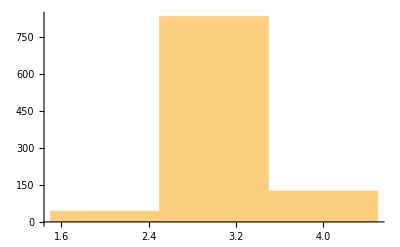

```mathematica
Histogram[%53]
```

```mathematica
N[Mean[Table[Abs[3-Position[d20[[x]],Min[d20[[x]]]][[1,1]]]/3,{x,1000}]]]
```

0.056